# Density of state

```mathematica
(*Equation of motion?*)
M=Flatten[Table[D[Subscript[ρ, n,m][t],t]==-I (Subscript[w, En][n,m])Subscript[ρ, n,m]+I/ℏ Sum[Subscript[d, n,v] Ε[n,v] Subscript[ρ, v,m]-Subscript[ρ, n,v] Subscript[d, v,m] Ε[v,m],{v,1,4}]+If[n≠m,-Subscript[γ, n,m] Subscript[ρ, n,m],Sum[If[n≥ 3,-Γ[v,n] Subscript[ρ, n,n],Γ[n,v] Subscript[ρ, v,v]],{v,1,4}]],{n,1,4},{m,1,4}]//Expand,1];
%//TableForm
```

ρ_(1,1)'[t]==ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]+(ⅈ d_(1,2) ρ_(2,1) Ε[1,2])/ℏ+(ⅈ d_(1,3) ρ_(3,1) Ε[1,3])/ℏ+(ⅈ d_(1,4) ρ_(4,1) Ε[1,4])/ℏ-(ⅈ d_(2,1) ρ_(1,2) Ε[2,1])/ℏ-(ⅈ d_(3,1) ρ_(1,3) Ε[3,1])/ℏ-(ⅈ d_(4,1) ρ_(1,4) Ε[4,1])/ℏ-ⅈ ρ_(1,1) w_En[1,1]
ρ_(1,2)'[t]==-γ_(1,2) ρ_(1,2)+(ⅈ d_(1,1) ρ_(1,2) Ε[1,1])/ℏ-(ⅈ d_(1,2) ρ_(1,1) Ε[1,2])/ℏ+(ⅈ d_(1,2) ρ_(2,2) Ε[1,2])/ℏ+(ⅈ d_(1,3) ρ_(3,2) Ε[1,3])/ℏ+(ⅈ d_(1,4) ρ_(4,2) Ε[1,4])/ℏ-(ⅈ d_(2,2) ρ_(1,2) Ε[2,2])/ℏ-(ⅈ d_(3,2) ρ_(1,3) Ε[3,2])/ℏ-(ⅈ d_(4,2) ρ_(1,4) Ε[4,2])/ℏ-ⅈ ρ_(1,2) w_En[1,2]
ρ_(1,3)'[t]==-γ_(1,3) ρ_(1,3)+(ⅈ d_(1,1) ρ_(1,3) Ε[1,1])/ℏ+(ⅈ d_(1,2) ρ_(2,3) Ε[1,2])/ℏ-(ⅈ d_(1,3) ρ_(1,1) Ε[1,3])/ℏ+(ⅈ d_(1,3) ρ_(3,3) Ε[1,3])/ℏ+(ⅈ d_(1,4) ρ_(4,3) Ε[1,4])/ℏ-(ⅈ d_(2,3) ρ_(1,2) Ε[2,3])/ℏ-(ⅈ d_(3,3) ρ_(1,3) Ε[3,3])/ℏ-(ⅈ d_(4,3) ρ_(1,4) Ε[4,3])/ℏ-ⅈ ρ_(1,3) w_En[1,3]
ρ_(1,4)'[t]==-γ_(1,4) ρ_(1,4)+(ⅈ d_(1,1) ρ_(1,4) Ε[1,1])/ℏ+(ⅈ d_(1,2) ρ_(2,4) Ε[1,2])/ℏ+(ⅈ d_(1,3) ρ_(3,4) Ε[1,3])/ℏ-(ⅈ d_(1,4) ρ_(1,1) Ε[1,4])/ℏ+(ⅈ d_(1,4) ρ_(4,4) Ε[1,4])/ℏ-(ⅈ d_(2,4) ρ_(1,2) Ε[2,4])/ℏ-(ⅈ d_(3,4) ρ_(1,3) Ε[3,4])/ℏ-(ⅈ d_(4,4) ρ_(1,4) Ε[4,4])/ℏ-ⅈ ρ_(1,4) w_En[1,4]
ρ_(2,1)'[t]==-γ_(2,1) ρ_(2,1)-(ⅈ d_(1,1) ρ_(2,1) Ε[1,1])/ℏ+(ⅈ d_(2,1) ρ_(1,1) Ε[2,1])/ℏ-(ⅈ d_(2,1) ρ_(2,2) Ε[2,1])/ℏ+(ⅈ d_(2,2) ρ_(2,1) Ε[2,2])/ℏ+(ⅈ d_(2,3) ρ_(3,1) Ε[2,3])/ℏ+(ⅈ d_(2,4) ρ_(4,1) Ε[2,4])/ℏ-(ⅈ d_(3,1) ρ_(2,3) Ε[3,1])/ℏ-(ⅈ d_(4,1) ρ_(2,4) Ε[4,1])/ℏ-ⅈ ρ_(2,1) w_En[2,1]
ρ_(2,2)'[t]==ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]-(ⅈ d_(1,2) ρ_(2,1) Ε[1,2])/ℏ+(ⅈ d_(2,1) ρ_(1,2) Ε[2,1])/ℏ+(ⅈ d_(2,3) ρ_(3,2) Ε[2,3])/ℏ+(ⅈ d_(2,4) ρ_(4,2) Ε[2,4])/ℏ-(ⅈ d_(3,2) ρ_(2,3) Ε[3,2])/ℏ-(ⅈ d_(4,2) ρ_(2,4) Ε[4,2])/ℏ-ⅈ ρ_(2,2) w_En[2,2]
ρ_(2,3)'[t]==-γ_(2,3) ρ_(2,3)-(ⅈ d_(1,3) ρ_(2,1) Ε[1,3])/ℏ+(ⅈ d_(2,1) ρ_(1,3) Ε[2,1])/ℏ+(ⅈ d_(2,2) ρ_(2,3) Ε[2,2])/ℏ-(ⅈ d_(2,3) ρ_(2,2) Ε[2,3])/ℏ+(ⅈ d_(2,3) ρ_(3,3) Ε[2,3])/ℏ+(ⅈ d_(2,4) ρ_(4,3) Ε[2,4])/ℏ-(ⅈ d_(3,3) ρ_(2,3) Ε[3,3])/ℏ-(ⅈ d_(4,3) ρ_(2,4) Ε[4,3])/ℏ-ⅈ ρ_(2,3) w_En[2,3]
ρ_(2,4)'[t]==-γ_(2,4) ρ_(2,4)-(ⅈ d_(1,4) ρ_(2,1) Ε[1,4])/ℏ+(ⅈ d_(2,1) ρ_(1,4) Ε[2,1])/ℏ+(ⅈ d_(2,2) ρ_(2,4) Ε[2,2])/ℏ+(ⅈ d_(2,3) ρ_(3,4) Ε[2,3])/ℏ-(ⅈ d_(2,4) ρ_(2,2) Ε[2,4])/ℏ+(ⅈ d_(2,4) ρ_(4,4) Ε[2,4])/ℏ-(ⅈ d_(3,4) ρ_(2,3) Ε[3,4])/ℏ-(ⅈ d_(4,4) ρ_(2,4) Ε[4,4])/ℏ-ⅈ ρ_(2,4) w_En[2,4]
ρ_(3,1)'[t]==-γ_(3,1) ρ_(3,1)-(ⅈ d_(1,1) ρ_(3,1) Ε[1,1])/ℏ-(ⅈ d_(2,1) ρ_(3,2) Ε[2,1])/ℏ+(ⅈ d_(3,1) ρ_(1,1) Ε[3,1])/ℏ-(ⅈ d_(3,1) ρ_(3,3) Ε[3,1])/ℏ+(ⅈ d_(3,2) ρ_(2,1) Ε[3,2])/ℏ+(ⅈ d_(3,3) ρ_(3,1) Ε[3,3])/ℏ+(ⅈ d_(3,4) ρ_(4,1) Ε[3,4])/ℏ-(ⅈ d_(4,1) ρ_(3,4) Ε[4,1])/ℏ-ⅈ ρ_(3,1) w_En[3,1]
ρ_(3,2)'[t]==-γ_(3,2) ρ_(3,2)-(ⅈ d_(1,2) ρ_(3,1) Ε[1,2])/ℏ-(ⅈ d_(2,2) ρ_(3,2) Ε[2,2])/ℏ+(ⅈ d_(3,1) ρ_(1,2) Ε[3,1])/ℏ+(ⅈ d_(3,2) ρ_(2,2) Ε[3,2])/ℏ-(ⅈ d_(3,2) ρ_(3,3) Ε[3,2])/ℏ+(ⅈ d_(3,3) ρ_(3,2) Ε[3,3])/ℏ+(ⅈ d_(3,4) ρ_(4,2) Ε[3,4])/ℏ-(ⅈ d_(4,2) ρ_(3,4) Ε[4,2])/ℏ-ⅈ ρ_(3,2) w_En[3,2]
ρ_(3,3)'[t]==-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]-ρ_(3,3) Γ[4,3]-(ⅈ d_(1,3) ρ_(3,1) Ε[1,3])/ℏ-(ⅈ d_(2,3) ρ_(3,2) Ε[2,3])/ℏ+(ⅈ d_(3,1) ρ_(1,3) Ε[3,1])/ℏ+(ⅈ d_(3,2) ρ_(2,3) Ε[3,2])/ℏ+(ⅈ d_(3,4) ρ_(4,3) Ε[3,4])/ℏ-(ⅈ d_(4,3) ρ_(3,4) Ε[4,3])/ℏ-ⅈ ρ_(3,3) w_En[3,3]
ρ_(3,4)'[t]==-γ_(3,4) ρ_(3,4)-(ⅈ d_(1,4) ρ_(3,1) Ε[1,4])/ℏ-(ⅈ d_(2,4) ρ_(3,2) Ε[2,4])/ℏ+(ⅈ d_(3,1) ρ_(1,4) Ε[3,1])/ℏ+(ⅈ d_(3,2) ρ_(2,4) Ε[3,2])/ℏ+(ⅈ d_(3,3) ρ_(3,4) Ε[3,3])/ℏ-(ⅈ d_(3,4) ρ_(3,3) Ε[3,4])/ℏ+(ⅈ d_(3,4) ρ_(4,4) Ε[3,4])/ℏ-(ⅈ d_(4,4) ρ_(3,4) Ε[4,4])/ℏ-ⅈ ρ_(3,4) w_En[3,4]
ρ_(4,1)'[t]==-γ_(4,1) ρ_(4,1)-(ⅈ d_(1,1) ρ_(4,1) Ε[1,1])/ℏ-(ⅈ d_(2,1) ρ_(4,2) Ε[2,1])/ℏ-(ⅈ d_(3,1) ρ_(4,3) Ε[3,1])/ℏ+(ⅈ d_(4,1) ρ_(1,1) Ε[4,1])/ℏ-(ⅈ d_(4,1) ρ_(4,4) Ε[4,1])/ℏ+(ⅈ d_(4,2) ρ_(2,1) Ε[4,2])/ℏ+(ⅈ d_(4,3) ρ_(3,1) Ε[4,3])/ℏ+(ⅈ d_(4,4) ρ_(4,1) Ε[4,4])/ℏ-ⅈ ρ_(4,1) w_En[4,1]
ρ_(4,2)'[t]==-γ_(4,2) ρ_(4,2)-(ⅈ d_(1,2) ρ_(4,1) Ε[1,2])/ℏ-(ⅈ d_(2,2) ρ_(4,2) Ε[2,2])/ℏ-(ⅈ d_(3,2) ρ_(4,3) Ε[3,2])/ℏ+(ⅈ d_(4,1) ρ_(1,2) Ε[4,1])/ℏ+(ⅈ d_(4,2) ρ_(2,2) Ε[4,2])/ℏ-(ⅈ d_(4,2) ρ_(4,4) Ε[4,2])/ℏ+(ⅈ d_(4,3) ρ_(3,2) Ε[4,3])/ℏ+(ⅈ d_(4,4) ρ_(4,2) Ε[4,4])/ℏ-ⅈ ρ_(4,2) w_En[4,2]
ρ_(4,3)'[t]==-γ_(4,3) ρ_(4,3)-(ⅈ d_(1,3) ρ_(4,1) Ε[1,3])/ℏ-(ⅈ d_(2,3) ρ_(4,2) Ε[2,3])/ℏ-(ⅈ d_(3,3) ρ_(4,3) Ε[3,3])/ℏ+(ⅈ d_(4,1) ρ_(1,3) Ε[4,1])/ℏ+(ⅈ d_(4,2) ρ_(2,3) Ε[4,2])/ℏ+(ⅈ d_(4,3) ρ_(3,3) Ε[4,3])/ℏ-(ⅈ d_(4,3) ρ_(4,4) Ε[4,3])/ℏ+(ⅈ d_(4,4) ρ_(4,3) Ε[4,4])/ℏ-ⅈ ρ_(4,3) w_En[4,3]
ρ_(4,4)'[t]==-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]-ρ_(4,4) Γ[3,4]-ρ_(4,4) Γ[4,4]-(ⅈ d_(1,4) ρ_(4,1) Ε[1,4])/ℏ-(ⅈ d_(2,4) ρ_(4,2) Ε[2,4])/ℏ-(ⅈ d_(3,4) ρ_(4,3) Ε[3,4])/ℏ+(ⅈ d_(4,1) ρ_(1,4) Ε[4,1])/ℏ+(ⅈ d_(4,2) ρ_(2,4) Ε[4,2])/ℏ+(ⅈ d_(4,3) ρ_(3,4) Ε[4,3])/ℏ-ⅈ ρ_(4,4) w_En[4,4]

```mathematica
(*Applying Electric field is E Exp[-Iwt]*)
Subscript[w, En][n_,m_]:=If[n>m,w[n,m],-w[m,n]]
Subscript[w, Ex][i_,j_]:=If[i>j,Subscript[w, Ext][i,j],-Subscript[w, Ext][j,i]]
M1=M/.Flatten[Table[ Ε[i,j]->E0[i,j]Exp[-I Subscript[w, Ex][i,j]t],{i,1,4},{j,1,4}]];
%//TableForm
```

ρ_(1,1)'[t]==-(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(1,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(4,1))/ℏ+ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]
ρ_(1,2)'[t]==-(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(1,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(1,2))/ℏ-γ_(1,2) ρ_(1,2)-(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(1,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(1,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(4,2))/ℏ+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(1,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(1,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(1,3))/ℏ-γ_(1,3) ρ_(1,3)-(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(1,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(4,3))/ℏ+ⅈ ρ_(1,3) w[3,1]
ρ_(1,4)'[t]==-(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(1,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(1,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(1,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(1,4))/ℏ-γ_(1,4) ρ_(1,4)+(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(4,4))/ℏ+ⅈ ρ_(1,4) w[4,1]
ρ_(2,1)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(2,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,1))/ℏ-γ_(2,1) ρ_(2,1)-(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(2,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(2,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(2,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(4,1))/ℏ-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,1))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(2,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(4,2))/ℏ+ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]
ρ_(2,3)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(2,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(2,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(2,3))/ℏ-γ_(2,3) ρ_(2,3)-(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(2,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(4,3))/ℏ+ⅈ ρ_(2,3) w[3,2]
ρ_(2,4)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(2,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(2,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(2,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(2,4))/ℏ-γ_(2,4) ρ_(2,4)+(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(4,4))/ℏ+ⅈ ρ_(2,4) w[4,2]
ρ_(3,1)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,1))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(3,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,1))/ℏ-γ_(3,1) ρ_(3,1)-(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(3,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(3,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(3,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(4,1))/ℏ-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,2))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(3,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(3,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,2))/ℏ-γ_(3,2) ρ_(3,2)-(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(3,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(3,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(4,2))/ℏ-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,3))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(3,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(4,3))/ℏ+ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]-ρ_(3,3) Γ[4,3]
ρ_(3,4)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,4))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(3,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(3,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(3,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(3,4))/ℏ-γ_(3,4) ρ_(3,4)+(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(4,4))/ℏ+ⅈ ρ_(3,4) w[4,3]
ρ_(4,1)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(1,1))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(2,1))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(3,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(4,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,1))/ℏ-γ_(4,1) ρ_(4,1)-(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(4,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(4,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(4,4))/ℏ-ⅈ ρ_(4,1) w[4,1]
ρ_(4,2)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(1,2))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(2,2))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(3,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(4,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(4,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,2))/ℏ-γ_(4,2) ρ_(4,2)-(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(4,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(4,4))/ℏ-ⅈ ρ_(4,2) w[4,2]
ρ_(4,3)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(1,3))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(2,3))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(3,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(4,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(4,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(4,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,3))/ℏ-γ_(4,3) ρ_(4,3)-(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(4,4))/ℏ-ⅈ ρ_(4,3) w[4,3]
ρ_(4,4)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(1,4))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(2,4))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(3,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(4,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(4,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(4,3))/ℏ+ⅈ ρ_(4,4) w[4,4]-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]-ρ_(4,4) Γ[3,4]-ρ_(4,4) Γ[4,4]

```mathematica
(*In terms of rabi frequency*)
M2=M1/.{Subscript[d, 3,1]->(ℏ Ω31)/(2 E0[3,1]),Subscript[d, 1,3]->(ℏ Ω13)/(2 E0[1,3]),Subscript[d, 4,1]->(ℏ Ω41)/(2 E0[4,1]),Subscript[d, 1,4]->(ℏ Ω14)/(2 E0[1,4]),Subscript[d, 3,2]->(ℏ Ω32)/(2 E0[3,2]),Subscript[d, 2,3]->(ℏ Ω23)/(2 E0[2,3]),Subscript[d, 4,2]->(ℏ Ω42)/(2 E0[4,2]),Subscript[d, 2,4]->(ℏ Ω24)/(2 E0[2,4]),Subscript[d, 1,2]->(ℏ Ω12)/(2 E0[1,2]),Subscript[d, 2,1]->(ℏ Ω21)/(2 E0[2,1]),Subscript[d, 3,4]->(ℏ Ω34)/(2 E0[3,4]),Subscript[d, 4,3]->(ℏ Ω43)/(2 E0[4,3])};
%//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)+ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]
ρ_(1,2)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(1,1)+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(1,2))/ℏ-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,2)+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(1,2)+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(1,3))/ℏ-γ_(1,3) ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,3)+ⅈ ρ_(1,3) w[3,1]
ρ_(1,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(1,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(1,3)+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(1,4))/ℏ-γ_(1,4) ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,4)+ⅈ ρ_(1,4) w[4,1]
ρ_(2,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,1)-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(2,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,1))/ℏ-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(2,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,1)-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)+ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]
ρ_(2,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(2,2)+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(2,3))/ℏ-γ_(2,3) ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,3)+ⅈ ρ_(2,3) w[3,2]
ρ_(2,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(2,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(2,3)+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(2,4))/ℏ-γ_(2,4) ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,4)+ⅈ ρ_(2,4) w[4,2]
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,1)-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(3,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,1))/ℏ-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,1)-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(3,1)-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(3,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,2))/ℏ-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,2)-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,3)+ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]-ρ_(3,3) Γ[4,3]
ρ_(3,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(3,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(3,3)+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(3,4))/ℏ-γ_(3,4) ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,4)+ⅈ ρ_(3,4) w[4,3]
ρ_(4,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,1)-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(4,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,1))/ℏ-γ_(4,1) ρ_(4,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(4,4)-ⅈ ρ_(4,1) w[4,1]
ρ_(4,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(4,1)-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(4,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,2))/ℏ-γ_(4,2) ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(4,4)-ⅈ ρ_(4,2) w[4,2]
ρ_(4,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(4,2)-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(4,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,3))/ℏ-γ_(4,3) ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(4,4)-ⅈ ρ_(4,3) w[4,3]
ρ_(4,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,3)+ⅈ ρ_(4,4) w[4,4]-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]-ρ_(4,4) Γ[3,4]-ρ_(4,4) Γ[4,4]

```mathematica
(*There is no dipole and w to themselves*)
M3=M2/.{Subscript[d, 1,1]->0,Subscript[d, 2,2]->0,Subscript[d, 3,3]->0,Subscript[d, 4,4]->0,Subscript[w, 1,1]->0,Subscript[w, 2,2]->0,Subscript[w, 3,3]->0,Subscript[w, 4,4]->0};
%//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)+ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]
ρ_(1,2)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(1,1)-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,2)+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(1,2)-γ_(1,3) ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,3)+ⅈ ρ_(1,3) w[3,1]
ρ_(1,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(1,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(1,3)-γ_(1,4) ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,4)+ⅈ ρ_(1,4) w[4,1]
ρ_(2,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,1)-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(2,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,1)-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)+ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]
ρ_(2,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(2,2)-γ_(2,3) ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,3)+ⅈ ρ_(2,3) w[3,2]
ρ_(2,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(2,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(2,3)-γ_(2,4) ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,4)+ⅈ ρ_(2,4) w[4,2]
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,1)-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,1)-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(3,1)-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,2)-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,3)+ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]-ρ_(3,3) Γ[4,3]
ρ_(3,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(3,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(3,3)-γ_(3,4) ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,4)+ⅈ ρ_(3,4) w[4,3]
ρ_(4,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,1)-γ_(4,1) ρ_(4,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(4,4)-ⅈ ρ_(4,1) w[4,1]
ρ_(4,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(4,1)-γ_(4,2) ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(4,4)-ⅈ ρ_(4,2) w[4,2]
ρ_(4,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(4,2)-γ_(4,3) ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(4,4)-ⅈ ρ_(4,3) w[4,3]
ρ_(4,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,3)+ⅈ ρ_(4,4) w[4,4]-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]-ρ_(4,4) Γ[3,4]-ρ_(4,4) Γ[4,4]

```mathematica
(*Limit 3->4 and 1->2 process*)
M4=M3/.{Ω21 ->0,Ω12 ->0,Ω34 ->0,Ω43 ->0};
%//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)+ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]
ρ_(1,2)'[t]==-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,2)+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(1,2)-γ_(1,3) ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,3)+ⅈ ρ_(1,3) w[3,1]
ρ_(1,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(1,2)-γ_(1,4) ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,4)+ⅈ ρ_(1,4) w[4,1]
ρ_(2,1)'[t]==-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,1)-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)+ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]
ρ_(2,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(2,2)-γ_(2,3) ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,3)+ⅈ ρ_(2,3) w[3,2]
ρ_(2,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(2,2)-γ_(2,4) ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,4)+ⅈ ρ_(2,4) w[4,2]
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,1)-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(3,4)-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,2)-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(3,4)-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]-ρ_(3,3) Γ[4,3]
ρ_(3,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(3,2)-γ_(3,4) ρ_(3,4)+ⅈ ρ_(3,4) w[4,3]
ρ_(4,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,1)-γ_(4,1) ρ_(4,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(4,4)-ⅈ ρ_(4,1) w[4,1]
ρ_(4,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,2)-γ_(4,2) ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(4,4)-ⅈ ρ_(4,2) w[4,2]
ρ_(4,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(4,2)-γ_(4,3) ρ_(4,3)-ⅈ ρ_(4,3) w[4,3]
ρ_(4,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)+ⅈ ρ_(4,4) w[4,4]-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]-ρ_(4,4) Γ[3,4]-ρ_(4,4) Γ[4,4]

```mathematica
(*No decay on 3->4 and 1->2, no self decay, no self frequncy*)
M5=M4/.{Γ[2,1]-> 0,Γ[1,2]-> 0,Γ[4,3]-> 0,Γ[3,4]-> 0,Γ[1,1]-> 0,Γ[2,2]-> 0,Γ[3,3]-> 0,Γ[4,4]-> 0,w[1,1]-> 0,w[2,2]->0,w[3,3]->0,w[4,4]->0};
%//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]
ρ_(1,2)'[t]==-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,2)+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(1,2)-γ_(1,3) ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,3)+ⅈ ρ_(1,3) w[3,1]
ρ_(1,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(1,2)-γ_(1,4) ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,4)+ⅈ ρ_(1,4) w[4,1]
ρ_(2,1)'[t]==-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,1)-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]
ρ_(2,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(2,2)-γ_(2,3) ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,3)+ⅈ ρ_(2,3) w[3,2]
ρ_(2,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(2,2)-γ_(2,4) ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,4)+ⅈ ρ_(2,4) w[4,2]
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,1)-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(3,4)-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,2)-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(3,4)-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]
ρ_(3,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(3,2)-γ_(3,4) ρ_(3,4)+ⅈ ρ_(3,4) w[4,3]
ρ_(4,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,1)-γ_(4,1) ρ_(4,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(4,4)-ⅈ ρ_(4,1) w[4,1]
ρ_(4,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,2)-γ_(4,2) ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(4,4)-ⅈ ρ_(4,2) w[4,2]
ρ_(4,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(4,2)-γ_(4,3) ρ_(4,3)-ⅈ ρ_(4,3) w[4,3]
ρ_(4,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]

```mathematica
(*Sending it to Rotating frame!*)
opt={
Subscript[w, Ext][1,1]-> 0,Subscript[w, Ext][2,2]->0,Subscript[w, Ext][3,3]->0,Subscript[w, Ext][4,4]->0,(*no freq itself*)
Subscript[w, Ext][2,1]-> Subscript[w, Ext][3,1]-Subscript[w, Ext][3,2],Subscript[w, Ext][4,3]->Subscript[w, Ext][4,2]-Subscript[w, Ext][3,2](*not allowed transition by other transition field*)
};
rot=Flatten[Table[D[Subscript[ρ, i,j][t],t]-> D[Subscript[σ, i,j][t]Exp[-I (Subscript[w, Ex][i,j])t],t],{i,1,4},{j,1,4}]/.opt]
rot1=Flatten[Table[Subscript[ρ, i,j]->Subscript[σ, i,j][t]Exp[-I (Subscript[w, Ex][i,j])t],{i,1,4},{j,1,4}]/.opt]
```

{ρ_(1,1)'[t]→σ_(1,1)'[t],ρ_(1,2)'[t]→ⅈ ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2])) (w_Ext[3,1]-w_Ext[3,2]) σ_(1,2)[t]+ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2])) σ_(1,2)'[t],ρ_(1,3)'[t]→ⅈ ⅇ^(ⅈ t w_Ext[3,1]) w_Ext[3,1] σ_(1,3)[t]+ⅇ^(ⅈ t w_Ext[3,1]) σ_(1,3)'[t],ρ_(1,4)'[t]→ⅈ ⅇ^(ⅈ t w_Ext[4,1]) w_Ext[4,1] σ_(1,4)[t]+ⅇ^(ⅈ t w_Ext[4,1]) σ_(1,4)'[t],ρ_(2,1)'[t]→-ⅈ ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2])) (w_Ext[3,1]-w_Ext[3,2]) σ_(2,1)[t]+ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2])) σ_(2,1)'[t],ρ_(2,2)'[t]→σ_(2,2)'[t],ρ_(2,3)'[t]→ⅈ ⅇ^(ⅈ t w_Ext[3,2]) w_Ext[3,2] σ_(2,3)[t]+ⅇ^(ⅈ t w_Ext[3,2]) σ_(2,3)'[t],ρ_(2,4)'[t]→ⅈ ⅇ^(ⅈ t w_Ext[4,2]) w_Ext[4,2] σ_(2,4)[t]+ⅇ^(ⅈ t w_Ext[4,2]) σ_(2,4)'[t],ρ_(3,1)'[t]→-ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) w_Ext[3,1] σ_(3,1)[t]+ⅇ^(-ⅈ t w_Ext[3,1]) σ_(3,1)'[t],ρ_(3,2)'[t]→-ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) w_Ext[3,2] σ_(3,2)[t]+ⅇ^(-ⅈ t w_Ext[3,2]) σ_(3,2)'[t],ρ_(3,3)'[t]→σ_(3,3)'[t],ρ_(3,4)'[t]→ⅈ ⅇ^(ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) (-w_Ext[3,2]+w_Ext[4,2]) σ_(3,4)[t]+ⅇ^(ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) σ_(3,4)'[t],ρ_(4,1)'[t]→-ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) w_Ext[4,1] σ_(4,1)[t]+ⅇ^(-ⅈ t w_Ext[4,1]) σ_(4,1)'[t],ρ_(4,2)'[t]→-ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) w_Ext[4,2] σ_(4,2)[t]+ⅇ^(-ⅈ t w_Ext[4,2]) σ_(4,2)'[t],ρ_(4,3)'[t]→-ⅈ ⅇ^(-ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) (-w_Ext[3,2]+w_Ext[4,2]) σ_(4,3)[t]+ⅇ^(-ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) σ_(4,3)'[t],ρ_(4,4)'[t]→σ_(4,4)'[t]}

{ρ_(1,1)→σ_(1,1)[t],ρ_(1,2)→ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2])) σ_(1,2)[t],ρ_(1,3)→ⅇ^(ⅈ t w_Ext[3,1]) σ_(1,3)[t],ρ_(1,4)→ⅇ^(ⅈ t w_Ext[4,1]) σ_(1,4)[t],ρ_(2,1)→ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2])) σ_(2,1)[t],ρ_(2,2)→σ_(2,2)[t],ρ_(2,3)→ⅇ^(ⅈ t w_Ext[3,2]) σ_(2,3)[t],ρ_(2,4)→ⅇ^(ⅈ t w_Ext[4,2]) σ_(2,4)[t],ρ_(3,1)→ⅇ^(-ⅈ t w_Ext[3,1]) σ_(3,1)[t],ρ_(3,2)→ⅇ^(-ⅈ t w_Ext[3,2]) σ_(3,2)[t],ρ_(3,3)→σ_(3,3)[t],ρ_(3,4)→ⅇ^(ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) σ_(3,4)[t],ρ_(4,1)→ⅇ^(-ⅈ t w_Ext[4,1]) σ_(4,1)[t],ρ_(4,2)→ⅇ^(-ⅈ t w_Ext[4,2]) σ_(4,2)[t],ρ_(4,3)→ⅇ^(-ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) σ_(4,3)[t],ρ_(4,4)→σ_(4,4)[t]}

```mathematica
M6=Flatten[Solve[M5/.rot/.rot1,Flatten[Table[Subscript[σ, i,j]'[t],{i,1,4},{j,1,4}]]]//Simplify];
%//TableForm
```

σ_(1,1)'[t]→1/2 (ⅈ (-Ω31 σ_(1,3)[t]-Ω41 σ_(1,4)[t]+Ω13 σ_(3,1)[t]+Ω14 σ_(4,1)[t])+2 (Γ[1,3] σ_(3,3)[t]+Γ[1,4] σ_(4,4)[t]))
σ_(1,2)'[t]→1/2 (-2 γ_(1,2) σ_(1,2)[t]+ⅈ (2 (w[2,1]-w_Ext[3,1]+w_Ext[3,2]) σ_(1,2)[t]-Ω32 σ_(1,3)[t]-ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω42 σ_(1,4)[t]+Ω13 σ_(3,2)[t]+ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω14 σ_(4,2)[t]))
σ_(1,3)'[t]→-1/2 ⅈ (Ω13 σ_(1,1)[t]+Ω23 σ_(1,2)[t]-2 ⅈ γ_(1,3) σ_(1,3)[t]-2 w[3,1] σ_(1,3)[t]+2 w_Ext[3,1] σ_(1,3)[t]-Ω13 σ_(3,3)[t]-ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω14 σ_(4,3)[t])
σ_(1,4)'[t]→-1/2 ⅈ (Ω14 σ_(1,1)[t]+ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω24 σ_(1,2)[t]-2 ⅈ γ_(1,4) σ_(1,4)[t]-2 w[4,1] σ_(1,4)[t]+2 w_Ext[4,1] σ_(1,4)[t]-ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω13 σ_(3,4)[t]-Ω14 σ_(4,4)[t])
σ_(2,1)'[t]→1/2 (-2 γ_(2,1) σ_(2,1)[t]-ⅈ (2 (w[2,1]-w_Ext[3,1]+w_Ext[3,2]) σ_(2,1)[t]+Ω31 σ_(2,3)[t]+ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω41 σ_(2,4)[t]-Ω23 σ_(3,1)[t]-ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω24 σ_(4,1)[t]))
σ_(2,2)'[t]→1/2 (ⅈ (-Ω32 σ_(2,3)[t]-Ω42 σ_(2,4)[t]+Ω23 σ_(3,2)[t]+Ω24 σ_(4,2)[t])+2 (Γ[2,3] σ_(3,3)[t]+Γ[2,4] σ_(4,4)[t]))
σ_(2,3)'[t]→-1/2 ⅈ (Ω13 σ_(2,1)[t]+Ω23 σ_(2,2)[t]-2 ⅈ γ_(2,3) σ_(2,3)[t]-2 w[3,2] σ_(2,3)[t]+2 w_Ext[3,2] σ_(2,3)[t]-Ω23 σ_(3,3)[t]-Ω24 σ_(4,3)[t])
σ_(2,4)'[t]→-1/2 ⅈ (ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω14 σ_(2,1)[t]+Ω24 σ_(2,2)[t]-2 ⅈ γ_(2,4) σ_(2,4)[t]-2 w[4,2] σ_(2,4)[t]+2 w_Ext[4,2] σ_(2,4)[t]-Ω23 σ_(3,4)[t]-Ω24 σ_(4,4)[t])
σ_(3,1)'[t]→1/2 ⅈ (Ω31 σ_(1,1)[t]+Ω32 σ_(2,1)[t]+2 ⅈ γ_(3,1) σ_(3,1)[t]-2 w[3,1] σ_(3,1)[t]+2 w_Ext[3,1] σ_(3,1)[t]-Ω31 σ_(3,3)[t]-ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω41 σ_(3,4)[t])
σ_(3,2)'[t]→1/2 ⅈ (Ω31 σ_(1,2)[t]+Ω32 σ_(2,2)[t]+2 ⅈ γ_(3,2) σ_(3,2)[t]-2 w[3,2] σ_(3,2)[t]+2 w_Ext[3,2] σ_(3,2)[t]-Ω32 σ_(3,3)[t]-Ω42 σ_(3,4)[t])
σ_(3,3)'[t]→1/2 ⅈ (Ω31 σ_(1,3)[t]+Ω32 σ_(2,3)[t]-Ω13 σ_(3,1)[t]-Ω23 σ_(3,2)[t]+2 ⅈ Γ[1,3] σ_(3,3)[t]+2 ⅈ Γ[2,3] σ_(3,3)[t])
σ_(3,4)'[t]→1/2 ⅈ (ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω31 σ_(1,4)[t]+Ω32 σ_(2,4)[t]-ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω14 σ_(3,1)[t]-Ω24 σ_(3,2)[t]+2 ⅈ γ_(3,4) σ_(3,4)[t]+2 w[4,3] σ_(3,4)[t]+2 w_Ext[3,2] σ_(3,4)[t]-2 w_Ext[4,2] σ_(3,4)[t])
σ_(4,1)'[t]→1/2 (ⅈ Ω41 σ_(1,1)[t]+ⅈ ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω42 σ_(2,1)[t]-2 γ_(4,1) σ_(4,1)[t]-2 ⅈ w[4,1] σ_(4,1)[t]+2 ⅈ w_Ext[4,1] σ_(4,1)[t]-ⅈ ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω31 σ_(4,3)[t]-ⅈ Ω41 σ_(4,4)[t])
σ_(4,2)'[t]→1/2 ⅈ (ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω41 σ_(1,2)[t]+Ω42 σ_(2,2)[t]+2 ⅈ γ_(4,2) σ_(4,2)[t]-2 w[4,2] σ_(4,2)[t]+2 w_Ext[4,2] σ_(4,2)[t]-Ω32 σ_(4,3)[t]-Ω42 σ_(4,4)[t])
σ_(4,3)'[t]→1/2 ⅈ (ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω41 σ_(1,3)[t]+Ω42 σ_(2,3)[t]-ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω13 σ_(4,1)[t]-Ω23 σ_(4,2)[t]+2 ⅈ γ_(4,3) σ_(4,3)[t]-2 w[4,3] σ_(4,3)[t]-2 w_Ext[3,2] σ_(4,3)[t]+2 w_Ext[4,2] σ_(4,3)[t])
σ_(4,4)'[t]→1/2 ⅈ (Ω41 σ_(1,4)[t]+Ω42 σ_(2,4)[t]-Ω14 σ_(4,1)[t]-Ω24 σ_(4,2)[t]+2 ⅈ Γ[1,4] σ_(4,4)[t]+2 ⅈ Γ[2,4] σ_(4,4)[t])

```mathematica
(*Some frequncy algebra*)
M7=M6/.{ⅇ^(ⅈ t (Subscript[w, Ext][3,1]-Subscript[w, Ext][3,2]-Subscript[w, Ext][4,1]+Subscript[w, Ext][4,2]))->1,ⅇ^(ⅈ t (-Subscript[w, Ext][3,1]+Subscript[w, Ext][3,2]+Subscript[w, Ext][4,1]-Subscript[w, Ext][4,2]))->1,(ⅇ^(-ⅈ t (Subscript[w, Ext][3,1]-Subscript[w, Ext][3,2]-Subscript[w, Ext][4,1]+Subscript[w, Ext][4,2])))->1}//Simplify;
%//TableForm
```

σ_(1,1)'[t]→1/2 (ⅈ (-Ω31 σ_(1,3)[t]-Ω41 σ_(1,4)[t]+Ω13 σ_(3,1)[t]+Ω14 σ_(4,1)[t])+2 (Γ[1,3] σ_(3,3)[t]+Γ[1,4] σ_(4,4)[t]))
σ_(1,2)'[t]→1/2 ⅈ (2 ⅈ γ_(1,2) σ_(1,2)[t]+2 (w[2,1]-w_Ext[3,1]+w_Ext[3,2]) σ_(1,2)[t]-Ω32 σ_(1,3)[t]-Ω42 σ_(1,4)[t]+Ω13 σ_(3,2)[t]+Ω14 σ_(4,2)[t])
σ_(1,3)'[t]→-1/2 ⅈ (Ω13 σ_(1,1)[t]+Ω23 σ_(1,2)[t]-2 ⅈ γ_(1,3) σ_(1,3)[t]-2 w[3,1] σ_(1,3)[t]+2 w_Ext[3,1] σ_(1,3)[t]-Ω13 σ_(3,3)[t]-Ω14 σ_(4,3)[t])
σ_(1,4)'[t]→1/2 ⅈ (-Ω14 σ_(1,1)[t]-Ω24 σ_(1,2)[t]+2 ⅈ γ_(1,4) σ_(1,4)[t]+2 w[4,1] σ_(1,4)[t]-2 w_Ext[4,1] σ_(1,4)[t]+Ω13 σ_(3,4)[t]+Ω14 σ_(4,4)[t])
σ_(2,1)'[t]→1/2 ⅈ (2 ⅈ γ_(2,1) σ_(2,1)[t]-2 (w[2,1]-w_Ext[3,1]+w_Ext[3,2]) σ_(2,1)[t]-Ω31 σ_(2,3)[t]-Ω41 σ_(2,4)[t]+Ω23 σ_(3,1)[t]+Ω24 σ_(4,1)[t])
σ_(2,2)'[t]→1/2 (ⅈ (-Ω32 σ_(2,3)[t]-Ω42 σ_(2,4)[t]+Ω23 σ_(3,2)[t]+Ω24 σ_(4,2)[t])+2 (Γ[2,3] σ_(3,3)[t]+Γ[2,4] σ_(4,4)[t]))
σ_(2,3)'[t]→-1/2 ⅈ (Ω13 σ_(2,1)[t]+Ω23 σ_(2,2)[t]-2 ⅈ γ_(2,3) σ_(2,3)[t]-2 w[3,2] σ_(2,3)[t]+2 w_Ext[3,2] σ_(2,3)[t]-Ω23 σ_(3,3)[t]-Ω24 σ_(4,3)[t])
σ_(2,4)'[t]→-1/2 ⅈ (Ω14 σ_(2,1)[t]+Ω24 σ_(2,2)[t]-2 ⅈ γ_(2,4) σ_(2,4)[t]-2 w[4,2] σ_(2,4)[t]+2 w_Ext[4,2] σ_(2,4)[t]-Ω23 σ_(3,4)[t]-Ω24 σ_(4,4)[t])
σ_(3,1)'[t]→1/2 ⅈ (Ω31 σ_(1,1)[t]+Ω32 σ_(2,1)[t]+2 ⅈ γ_(3,1) σ_(3,1)[t]-2 w[3,1] σ_(3,1)[t]+2 w_Ext[3,1] σ_(3,1)[t]-Ω31 σ_(3,3)[t]-Ω41 σ_(3,4)[t])
σ_(3,2)'[t]→1/2 ⅈ (Ω31 σ_(1,2)[t]+Ω32 σ_(2,2)[t]+2 ⅈ γ_(3,2) σ_(3,2)[t]-2 w[3,2] σ_(3,2)[t]+2 w_Ext[3,2] σ_(3,2)[t]-Ω32 σ_(3,3)[t]-Ω42 σ_(3,4)[t])
σ_(3,3)'[t]→1/2 ⅈ (Ω31 σ_(1,3)[t]+Ω32 σ_(2,3)[t]-Ω13 σ_(3,1)[t]-Ω23 σ_(3,2)[t]+2 ⅈ Γ[1,3] σ_(3,3)[t]+2 ⅈ Γ[2,3] σ_(3,3)[t])
σ_(3,4)'[t]→1/2 ⅈ (Ω31 σ_(1,4)[t]+Ω32 σ_(2,4)[t]-Ω14 σ_(3,1)[t]-Ω24 σ_(3,2)[t]+2 ⅈ γ_(3,4) σ_(3,4)[t]+2 w[4,3] σ_(3,4)[t]+2 w_Ext[3,2] σ_(3,4)[t]-2 w_Ext[4,2] σ_(3,4)[t])
σ_(4,1)'[t]→1/2 ⅈ (Ω41 σ_(1,1)[t]+Ω42 σ_(2,1)[t]+2 ⅈ γ_(4,1) σ_(4,1)[t]-2 w[4,1] σ_(4,1)[t]+2 w_Ext[4,1] σ_(4,1)[t]-Ω31 σ_(4,3)[t]-Ω41 σ_(4,4)[t])
σ_(4,2)'[t]→1/2 ⅈ (Ω41 σ_(1,2)[t]+Ω42 σ_(2,2)[t]+2 ⅈ γ_(4,2) σ_(4,2)[t]-2 w[4,2] σ_(4,2)[t]+2 w_Ext[4,2] σ_(4,2)[t]-Ω32 σ_(4,3)[t]-Ω42 σ_(4,4)[t])
σ_(4,3)'[t]→1/2 ⅈ (Ω41 σ_(1,3)[t]+Ω42 σ_(2,3)[t]-Ω13 σ_(4,1)[t]-Ω23 σ_(4,2)[t]+2 ⅈ γ_(4,3) σ_(4,3)[t]-2 w[4,3] σ_(4,3)[t]-2 w_Ext[3,2] σ_(4,3)[t]+2 w_Ext[4,2] σ_(4,3)[t])
σ_(4,4)'[t]→1/2 ⅈ (Ω41 σ_(1,4)[t]+Ω42 σ_(2,4)[t]-Ω14 σ_(4,1)[t]-Ω24 σ_(4,2)[t]+2 ⅈ Γ[1,4] σ_(4,4)[t]+2 ⅈ Γ[2,4] σ_(4,4)[t])

```mathematica
(*Let's Look at the difference of the frequncy*)
twophoton={w[2,1]-> Subscript[w, Ext][3,1]+Δ1-Subscript[w, Ext][3,2]-Δ3, w[4,3] ->-  Subscript[w, Ext][3,2] -Δ3+ Subscript[w, Ext][4,2]+Δ4};
onephoton={ w[3,1]->  Subscript[w, Ext][3,1]+Δ1,w[4,1] ->  Subscript[w, Ext][4,1]+Δ2,w[3,2]->  Subscript[w, Ext][3,2]+Δ3 , w[4,2] ->  Subscript[w, Ext][4,2] +Δ4};
M8=Simplify[Expand[M7/.twophoton/.onephoton]];
%//TableForm
```

σ_(1,1)'[t]→-1/2 ⅈ (Ω31 σ_(1,3)[t]+Ω41 σ_(1,4)[t]-Ω13 σ_(3,1)[t]+2 ⅈ Γ[1,3] σ_(3,3)[t]-Ω14 σ_(4,1)[t]+2 ⅈ Γ[1,4] σ_(4,4)[t])
σ_(1,2)'[t]→1/2 ⅈ (2 (Δ1-Δ3+ⅈ γ_(1,2)) σ_(1,2)[t]-Ω32 σ_(1,3)[t]-Ω42 σ_(1,4)[t]+Ω13 σ_(3,2)[t]+Ω14 σ_(4,2)[t])
σ_(1,3)'[t]→1/2 ⅈ (-Ω13 σ_(1,1)[t]-Ω23 σ_(1,2)[t]+2 Δ1 σ_(1,3)[t]+2 ⅈ γ_(1,3) σ_(1,3)[t]+Ω13 σ_(3,3)[t]+Ω14 σ_(4,3)[t])
σ_(1,4)'[t]→1/2 ⅈ (-Ω14 σ_(1,1)[t]-Ω24 σ_(1,2)[t]+2 Δ2 σ_(1,4)[t]+2 ⅈ γ_(1,4) σ_(1,4)[t]+Ω13 σ_(3,4)[t]+Ω14 σ_(4,4)[t])
σ_(2,1)'[t]→-1/2 ⅈ (2 (Δ1-Δ3-ⅈ γ_(2,1)) σ_(2,1)[t]+Ω31 σ_(2,3)[t]+Ω41 σ_(2,4)[t]-Ω23 σ_(3,1)[t]-Ω24 σ_(4,1)[t])
σ_(2,2)'[t]→-1/2 ⅈ (Ω32 σ_(2,3)[t]+Ω42 σ_(2,4)[t]-Ω23 σ_(3,2)[t]+2 ⅈ Γ[2,3] σ_(3,3)[t]-Ω24 σ_(4,2)[t]+2 ⅈ Γ[2,4] σ_(4,4)[t])
σ_(2,3)'[t]→1/2 ⅈ (-Ω13 σ_(2,1)[t]-Ω23 σ_(2,2)[t]+2 Δ3 σ_(2,3)[t]+2 ⅈ γ_(2,3) σ_(2,3)[t]+Ω23 σ_(3,3)[t]+Ω24 σ_(4,3)[t])
σ_(2,4)'[t]→1/2 ⅈ (-Ω14 σ_(2,1)[t]-Ω24 σ_(2,2)[t]+2 Δ4 σ_(2,4)[t]+2 ⅈ γ_(2,4) σ_(2,4)[t]+Ω23 σ_(3,4)[t]+Ω24 σ_(4,4)[t])
σ_(3,1)'[t]→1/2 ⅈ (Ω31 σ_(1,1)[t]+Ω32 σ_(2,1)[t]-2 Δ1 σ_(3,1)[t]+2 ⅈ γ_(3,1) σ_(3,1)[t]-Ω31 σ_(3,3)[t]-Ω41 σ_(3,4)[t])
σ_(3,2)'[t]→1/2 ⅈ (Ω31 σ_(1,2)[t]+Ω32 σ_(2,2)[t]-2 Δ3 σ_(3,2)[t]+2 ⅈ γ_(3,2) σ_(3,2)[t]-Ω32 σ_(3,3)[t]-Ω42 σ_(3,4)[t])
σ_(3,3)'[t]→1/2 ⅈ (Ω31 σ_(1,3)[t]+Ω32 σ_(2,3)[t]-Ω13 σ_(3,1)[t]-Ω23 σ_(3,2)[t]+2 ⅈ Γ[1,3] σ_(3,3)[t]+2 ⅈ Γ[2,3] σ_(3,3)[t])
σ_(3,4)'[t]→1/2 ⅈ (Ω31 σ_(1,4)[t]+Ω32 σ_(2,4)[t]-Ω14 σ_(3,1)[t]-Ω24 σ_(3,2)[t]-2 Δ3 σ_(3,4)[t]+2 Δ4 σ_(3,4)[t]+2 ⅈ γ_(3,4) σ_(3,4)[t])
σ_(4,1)'[t]→1/2 ⅈ (Ω41 σ_(1,1)[t]+Ω42 σ_(2,1)[t]-2 Δ2 σ_(4,1)[t]+2 ⅈ γ_(4,1) σ_(4,1)[t]-Ω31 σ_(4,3)[t]-Ω41 σ_(4,4)[t])
σ_(4,2)'[t]→1/2 ⅈ (Ω41 σ_(1,2)[t]+Ω42 σ_(2,2)[t]-2 Δ4 σ_(4,2)[t]+2 ⅈ γ_(4,2) σ_(4,2)[t]-Ω32 σ_(4,3)[t]-Ω42 σ_(4,4)[t])
σ_(4,3)'[t]→1/2 ⅈ (Ω41 σ_(1,3)[t]+Ω42 σ_(2,3)[t]-Ω13 σ_(4,1)[t]-Ω23 σ_(4,2)[t]+2 Δ3 σ_(4,3)[t]-2 Δ4 σ_(4,3)[t]+2 ⅈ γ_(4,3) σ_(4,3)[t])
σ_(4,4)'[t]→1/2 ⅈ (Ω41 σ_(1,4)[t]+Ω42 σ_(2,4)[t]-Ω14 σ_(4,1)[t]-Ω24 σ_(4,2)[t]+2 ⅈ Γ[1,4] σ_(4,4)[t]+2 ⅈ Γ[2,4] σ_(4,4)[t])

```mathematica
(*Now make this into two field*)
opt1={Δ2-> w43+Δ1,Δ4-> w43+Δ3,Ω41->Sqrt[7/2]Ω31,Ω14->Sqrt[7/2]Ω13,Ω42->Sqrt[4/5]Ω32,Ω24->Sqrt[4/5]Ω23};
(*Two Photon detuning*)
opt2={Δ3-> δ+Δ1};
M9=M8/.opt1/.opt2//Expand;
%//TableForm
```

σ_(1,1)'[t]→-1/2 ⅈ Ω31 σ_(1,3)[t]-1/2 ⅈ Ω41 σ_(1,4)[t]+1/2 ⅈ Ω13 σ_(3,1)[t]+Γ[1,3] σ_(3,3)[t]+1/2 ⅈ Ω14 σ_(4,1)[t]+Γ[1,4] σ_(4,4)[t]
σ_(1,2)'[t]→-ⅈ δ σ_(1,2)[t]-γ_(1,2) σ_(1,2)[t]-1/2 ⅈ Ω32 σ_(1,3)[t]-1/2 ⅈ Ω42 σ_(1,4)[t]+1/2 ⅈ Ω13 σ_(3,2)[t]+1/2 ⅈ Ω14 σ_(4,2)[t]
σ_(1,3)'[t]→-1/2 ⅈ Ω13 σ_(1,1)[t]-1/2 ⅈ Ω23 σ_(1,2)[t]+ⅈ Δ1 σ_(1,3)[t]-γ_(1,3) σ_(1,3)[t]+1/2 ⅈ Ω13 σ_(3,3)[t]+1/2 ⅈ Ω14 σ_(4,3)[t]
σ_(1,4)'[t]→-1/2 ⅈ Ω14 σ_(1,1)[t]-1/2 ⅈ Ω24 σ_(1,2)[t]+ⅈ w43 σ_(1,4)[t]+ⅈ Δ1 σ_(1,4)[t]-γ_(1,4) σ_(1,4)[t]+1/2 ⅈ Ω13 σ_(3,4)[t]+1/2 ⅈ Ω14 σ_(4,4)[t]
σ_(2,1)'[t]→ⅈ δ σ_(2,1)[t]-γ_(2,1) σ_(2,1)[t]-1/2 ⅈ Ω31 σ_(2,3)[t]-1/2 ⅈ Ω41 σ_(2,4)[t]+1/2 ⅈ Ω23 σ_(3,1)[t]+1/2 ⅈ Ω24 σ_(4,1)[t]
σ_(2,2)'[t]→-1/2 ⅈ Ω32 σ_(2,3)[t]-1/2 ⅈ Ω42 σ_(2,4)[t]+1/2 ⅈ Ω23 σ_(3,2)[t]+Γ[2,3] σ_(3,3)[t]+1/2 ⅈ Ω24 σ_(4,2)[t]+Γ[2,4] σ_(4,4)[t]
σ_(2,3)'[t]→-1/2 ⅈ Ω13 σ_(2,1)[t]-1/2 ⅈ Ω23 σ_(2,2)[t]+ⅈ δ σ_(2,3)[t]+ⅈ Δ1 σ_(2,3)[t]-γ_(2,3) σ_(2,3)[t]+1/2 ⅈ Ω23 σ_(3,3)[t]+1/2 ⅈ Ω24 σ_(4,3)[t]
σ_(2,4)'[t]→-1/2 ⅈ Ω14 σ_(2,1)[t]-1/2 ⅈ Ω24 σ_(2,2)[t]+ⅈ w43 σ_(2,4)[t]+ⅈ δ σ_(2,4)[t]+ⅈ Δ1 σ_(2,4)[t]-γ_(2,4) σ_(2,4)[t]+1/2 ⅈ Ω23 σ_(3,4)[t]+1/2 ⅈ Ω24 σ_(4,4)[t]
σ_(3,1)'[t]→1/2 ⅈ Ω31 σ_(1,1)[t]+1/2 ⅈ Ω32 σ_(2,1)[t]-ⅈ Δ1 σ_(3,1)[t]-γ_(3,1) σ_(3,1)[t]-1/2 ⅈ Ω31 σ_(3,3)[t]-1/2 ⅈ Ω41 σ_(3,4)[t]
σ_(3,2)'[t]→1/2 ⅈ Ω31 σ_(1,2)[t]+1/2 ⅈ Ω32 σ_(2,2)[t]-ⅈ δ σ_(3,2)[t]-ⅈ Δ1 σ_(3,2)[t]-γ_(3,2) σ_(3,2)[t]-1/2 ⅈ Ω32 σ_(3,3)[t]-1/2 ⅈ Ω42 σ_(3,4)[t]
σ_(3,3)'[t]→1/2 ⅈ Ω31 σ_(1,3)[t]+1/2 ⅈ Ω32 σ_(2,3)[t]-1/2 ⅈ Ω13 σ_(3,1)[t]-1/2 ⅈ Ω23 σ_(3,2)[t]-Γ[1,3] σ_(3,3)[t]-Γ[2,3] σ_(3,3)[t]
σ_(3,4)'[t]→1/2 ⅈ Ω31 σ_(1,4)[t]+1/2 ⅈ Ω32 σ_(2,4)[t]-1/2 ⅈ Ω14 σ_(3,1)[t]-1/2 ⅈ Ω24 σ_(3,2)[t]+ⅈ w43 σ_(3,4)[t]-γ_(3,4) σ_(3,4)[t]
σ_(4,1)'[t]→1/2 ⅈ Ω41 σ_(1,1)[t]+1/2 ⅈ Ω42 σ_(2,1)[t]-ⅈ w43 σ_(4,1)[t]-ⅈ Δ1 σ_(4,1)[t]-γ_(4,1) σ_(4,1)[t]-1/2 ⅈ Ω31 σ_(4,3)[t]-1/2 ⅈ Ω41 σ_(4,4)[t]
σ_(4,2)'[t]→1/2 ⅈ Ω41 σ_(1,2)[t]+1/2 ⅈ Ω42 σ_(2,2)[t]-ⅈ w43 σ_(4,2)[t]-ⅈ δ σ_(4,2)[t]-ⅈ Δ1 σ_(4,2)[t]-γ_(4,2) σ_(4,2)[t]-1/2 ⅈ Ω32 σ_(4,3)[t]-1/2 ⅈ Ω42 σ_(4,4)[t]
σ_(4,3)'[t]→1/2 ⅈ Ω41 σ_(1,3)[t]+1/2 ⅈ Ω42 σ_(2,3)[t]-1/2 ⅈ Ω13 σ_(4,1)[t]-1/2 ⅈ Ω23 σ_(4,2)[t]-ⅈ w43 σ_(4,3)[t]-γ_(4,3) σ_(4,3)[t]
σ_(4,4)'[t]→1/2 ⅈ Ω41 σ_(1,4)[t]+1/2 ⅈ Ω42 σ_(2,4)[t]-1/2 ⅈ Ω14 σ_(4,1)[t]-1/2 ⅈ Ω24 σ_(4,2)[t]-Γ[1,4] σ_(4,4)[t]-Γ[2,4] σ_(4,4)[t]

```mathematica
Table[(M9[[All,2]]/.Flatten[Table[{Subscript[σ, i,j][t]->Subscript[σ, i,j],Subscript[γ, i,j]->ToExpression["γ"<>ToString[i]<>ToString[j]],Γ[i,j]->ToExpression["Γ"<>ToString[i]<>ToString[j]]},{i,1,4},{j,1,4}]])[[i]],{i,1,16}]//FullSimplify
```

{-1/2 ⅈ (Ω31 σ_(1,3)+Ω41 σ_(1,4)-Ω13 σ_(3,1)+2 ⅈ Γ13 σ_(3,3)-Ω14 σ_(4,1)+2 ⅈ Γ14 σ_(4,4)),1/2 (-2 (γ12+ⅈ δ) σ_(1,2)+ⅈ (-Ω32 σ_(1,3)-Ω42 σ_(1,4)+Ω13 σ_(3,2)+Ω14 σ_(4,2))),-1/2 ⅈ (Ω13 σ_(1,1)+Ω23 σ_(1,2)+(-2 ⅈ γ13-2 Δ1) σ_(1,3)-Ω13 σ_(3,3)-Ω14 σ_(4,3)),1/2 ⅈ (-Ω14 σ_(1,1)-Ω24 σ_(1,2)+2 (w43+ⅈ γ14+Δ1) σ_(1,4)+Ω13 σ_(3,4)+Ω14 σ_(4,4)),1/2 (-2 (γ21-ⅈ δ) σ_(2,1)+ⅈ (-Ω31 σ_(2,3)-Ω41 σ_(2,4)+Ω23 σ_(3,1)+Ω24 σ_(4,1))),-1/2 ⅈ (Ω32 σ_(2,3)+Ω42 σ_(2,4)-Ω23 σ_(3,2)+2 ⅈ Γ23 σ_(3,3)-Ω24 σ_(4,2)+2 ⅈ Γ24 σ_(4,4)),-1/2 ⅈ (Ω13 σ_(2,1)+(-2 ⅈ γ23-2 (δ+Δ1)) σ_(2,3)+Ω23 (σ_(2,2)-σ_(3,3))-Ω24 σ_(4,3)),1/2 ⅈ (-Ω14 σ_(2,1)-Ω24 σ_(2,2)+2 (w43+ⅈ γ24+δ+Δ1) σ_(2,4)+Ω23 σ_(3,4)+Ω24 σ_(4,4)),1/2 ⅈ (Ω31 σ_(1,1)+Ω32 σ_(2,1)+2 ⅈ (γ31+ⅈ Δ1) σ_(3,1)-Ω31 σ_(3,3)-Ω41 σ_(3,4)),1/2 ⅈ (Ω31 σ_(1,2)+Ω32 σ_(2,2)+2 ⅈ (γ32+ⅈ (δ+Δ1)) σ_(3,2)-Ω32 σ_(3,3)-Ω42 σ_(3,4)),1/2 ⅈ (Ω31 σ_(1,3)+Ω32 σ_(2,3)-Ω13 σ_(3,1)-Ω23 σ_(3,2))-(Γ13+Γ23) σ_(3,3),1/2 ⅈ (Ω31 σ_(1,4)+Ω32 σ_(2,4)-Ω14 σ_(3,1)-Ω24 σ_(3,2)+2 (w43+ⅈ γ34) σ_(3,4)),-1/2 ⅈ (-Ω41 σ_(1,1)-Ω42 σ_(2,1)+2 (w43-ⅈ γ41+Δ1) σ_(4,1)+Ω31 σ_(4,3)+Ω41 σ_(4,4)),-1/2 ⅈ (-Ω41 σ_(1,2)-Ω42 σ_(2,2)+2 (w43-ⅈ γ42+δ+Δ1) σ_(4,2)+Ω32 σ_(4,3)+Ω42 σ_(4,4)),1/2 ⅈ (Ω41 σ_(1,3)+Ω42 σ_(2,3)-Ω13 σ_(4,1)-Ω23 σ_(4,2)-2 (w43-ⅈ γ43) σ_(4,3)),1/2 ⅈ (Ω41 σ_(1,4)+Ω42 σ_(2,4)-Ω14 σ_(4,1)-Ω24 σ_(4,2))-(Γ14+Γ24) σ_(4,4)}

```mathematica
(*Steady State Solution*)
M10=Table[(M9[[All,2]]/.Flatten[Table[{Subscript[σ, i,j][t]->Subscript[σ, i,j],Subscript[γ, i,j]->ToExpression["γ"<>ToString[i]<>ToString[j]],Γ[i,j]->ToExpression["Γ"<>ToString[i]<>ToString[j]]},{i,1,4},{j,1,4}]])[[i]]==0,{i,1,16}];
%//TableForm
```

```mathematica
{{-1/2 ⅈ Ω31 Subscript[σ, 1,3]-1/2 ⅈ Ω41 Subscript[σ, 1,4]+1/2 ⅈ Ω13 Subscript[σ, 3,1]+Γ13 Subscript[σ, 3,3]+1/2 ⅈ Ω14 Subscript[σ, 4,1]+Γ14 Subscript[σ, 4,4]==0}, {-γ12 Subscript[σ, 1,2]-ⅈ δ Subscript[σ, 1,2]-1/2 ⅈ Ω32 Subscript[σ, 1,3]-1/2 ⅈ Ω42 Subscript[σ, 1,4]+1/2 ⅈ Ω13 Subscript[σ, 3,2]+1/2 ⅈ Ω14 Subscript[σ, 4,2]==0}, {-1/2 ⅈ Ω13 Subscript[σ, 1,1]-1/2 ⅈ Ω23 Subscript[σ, 1,2]-γ13 Subscript[σ, 1,3]+ⅈ Δ1 Subscript[σ, 1,3]+1/2 ⅈ Ω13 Subscript[σ, 3,3]+1/2 ⅈ Ω14 Subscript[σ, 4,3]==0}, {-1/2 ⅈ Ω14 Subscript[σ, 1,1]-1/2 ⅈ Ω24 Subscript[σ, 1,2]+ⅈ w43 Subscript[σ, 1,4]-γ14 Subscript[σ, 1,4]+ⅈ Δ1 Subscript[σ, 1,4]+1/2 ⅈ Ω13 Subscript[σ, 3,4]+1/2 ⅈ Ω14 Subscript[σ, 4,4]==0}, {-γ21 Subscript[σ, 2,1]+ⅈ δ Subscript[σ, 2,1]-1/2 ⅈ Ω31 Subscript[σ, 2,3]-1/2 ⅈ Ω41 Subscript[σ, 2,4]+1/2 ⅈ Ω23 Subscript[σ, 3,1]+1/2 ⅈ Ω24 Subscript[σ, 4,1]==0}, {-1/2 ⅈ Ω32 Subscript[σ, 2,3]-1/2 ⅈ Ω42 Subscript[σ, 2,4]+1/2 ⅈ Ω23 Subscript[σ, 3,2]+Γ23 Subscript[σ, 3,3]+1/2 ⅈ Ω24 Subscript[σ, 4,2]+Γ24 Subscript[σ, 4,4]==0}, {-1/2 ⅈ Ω13 Subscript[σ, 2,1]-1/2 ⅈ Ω23 Subscript[σ, 2,2]-γ23 Subscript[σ, 2,3]+ⅈ δ Subscript[σ, 2,3]+ⅈ Δ1 Subscript[σ, 2,3]+1/2 ⅈ Ω23 Subscript[σ, 3,3]+1/2 ⅈ Ω24 Subscript[σ, 4,3]==0}, {-1/2 ⅈ Ω14 Subscript[σ, 2,1]-1/2 ⅈ Ω24 Subscript[σ, 2,2]+ⅈ w43 Subscript[σ, 2,4]-γ24 Subscript[σ, 2,4]+ⅈ δ Subscript[σ, 2,4]+ⅈ Δ1 Subscript[σ, 2,4]+1/2 ⅈ Ω23 Subscript[σ, 3,4]+1/2 ⅈ Ω24 Subscript[σ, 4,4]==0}, {1/2 ⅈ Ω31 Subscript[σ, 1,1]+1/2 ⅈ Ω32 Subscript[σ, 2,1]-γ31 Subscript[σ, 3,1]-ⅈ Δ1 Subscript[σ, 3,1]-1/2 ⅈ Ω31 Subscript[σ, 3,3]-1/2 ⅈ Ω41 Subscript[σ, 3,4]==0}, {1/2 ⅈ Ω31 Subscript[σ, 1,2]+1/2 ⅈ Ω32 Subscript[σ, 2,2]-γ32 Subscript[σ, 3,2]-ⅈ δ Subscript[σ, 3,2]-ⅈ Δ1 Subscript[σ, 3,2]-1/2 ⅈ Ω32 Subscript[σ, 3,3]-1/2 ⅈ Ω42 Subscript[σ, 3,4]==0}, {1/2 ⅈ Ω31 Subscript[σ, 1,3]+1/2 ⅈ Ω32 Subscript[σ, 2,3]-1/2 ⅈ Ω13 Subscript[σ, 3,1]-1/2 ⅈ Ω23 Subscript[σ, 3,2]-Γ13 Subscript[σ, 3,3]-Γ23 Subscript[σ, 3,3]==0}, {1/2 ⅈ Ω31 Subscript[σ, 1,4]+1/2 ⅈ Ω32 Subscript[σ, 2,4]-1/2 ⅈ Ω14 Subscript[σ, 3,1]-1/2 ⅈ Ω24 Subscript[σ, 3,2]+ⅈ w43 Subscript[σ, 3,4]-γ34 Subscript[σ, 3,4]==0}, {1/2 ⅈ Ω41 Subscript[σ, 1,1]+1/2 ⅈ Ω42 Subscript[σ, 2,1]-ⅈ w43 Subscript[σ, 4,1]-γ41 Subscript[σ, 4,1]-ⅈ Δ1 Subscript[σ, 4,1]-1/2 ⅈ Ω31 Subscript[σ, 4,3]-1/2 ⅈ Ω41 Subscript[σ, 4,4]==0}, {1/2 ⅈ Ω41 Subscript[σ, 1,2]+1/2 ⅈ Ω42 Subscript[σ, 2,2]-ⅈ w43 Subscript[σ, 4,2]-γ42 Subscript[σ, 4,2]-ⅈ δ Subscript[σ, 4,2]-ⅈ Δ1 Subscript[σ, 4,2]-1/2 ⅈ Ω32 Subscript[σ, 4,3]-1/2 ⅈ Ω42 Subscript[σ, 4,4]==0}, {1/2 ⅈ Ω41 Subscript[σ, 1,3]+1/2 ⅈ Ω42 Subscript[σ, 2,3]-1/2 ⅈ Ω13 Subscript[σ, 4,1]-1/2 ⅈ Ω23 Subscript[σ, 4,2]-ⅈ w43 Subscript[σ, 4,3]-γ43 Subscript[σ, 4,3]==0}, {1/2 ⅈ Ω41 Subscript[σ, 1,4]+1/2 ⅈ Ω42 Subscript[σ, 2,4]-1/2 ⅈ Ω14 Subscript[σ, 4,1]-1/2 ⅈ Ω24 Subscript[σ, 4,2]-Γ14 Subscript[σ, 4,4]-Γ24 Subscript[σ, 4,4]==0}}
```

```mathematica
43
1/2 ⅈ Ω41 Subscript[σ, 1,3]+1/2 ⅈ Ω42 Subscript[σ, 2,3]-1/2 ⅈ Ω13 Subscript[σ, 4,1]-1/2 ⅈ Ω23 Subscript[σ, 4,2]-ⅈ w43 Subscript[σ, 4,3]-γ43 Subscript[σ, 4,3]==0
42
1/2 ⅈ Ω41 Subscript[σ, 1,2]+1/2 ⅈ Ω42 Subscript[σ, 2,2]-ⅈ w43 Subscript[σ, 4,2]-γ42 Subscript[σ, 4,2]-ⅈ δ Subscript[σ, 4,2]-ⅈ Δ1 Subscript[σ, 4,2]-1/2 ⅈ Ω32 Subscript[σ, 4,3]-1/2 ⅈ Ω42 Subscript[σ, 4,4]==0
41
1/2 ⅈ Ω41 Subscript[σ, 1,1]+1/2 ⅈ Ω42 Subscript[σ, 2,1]-ⅈ w43 Subscript[σ, 4,1]-γ41 Subscript[σ, 4,1]-ⅈ Δ1 Subscript[σ, 4,1]-1/2 ⅈ Ω31 Subscript[σ, 4,3]-1/2 ⅈ Ω41 Subscript[σ, 4,4]==0
32
```

43

1/2 ⅈ Ω41 σ_(1,3)+1/2 ⅈ Ω42 σ_(2,3)-1/2 ⅈ Ω13 σ_(4,1)-1/2 ⅈ Ω23 σ_(4,2)-ⅈ w43 σ_(4,3)-γ43 σ_(4,3)==0

42

1/2 ⅈ Ω41 σ_(1,2)+1/2 ⅈ Ω42 σ_(2,2)-ⅈ w43 σ_(4,2)-γ42 σ_(4,2)-ⅈ δ σ_(4,2)-ⅈ Δ1 σ_(4,2)-1/2 ⅈ Ω32 σ_(4,3)-1/2 ⅈ Ω42 σ_(4,4)==0

41

1/2 ⅈ Ω41 σ_(1,1)+1/2 ⅈ Ω42 σ_(2,1)-ⅈ w43 σ_(4,1)-γ41 σ_(4,1)-ⅈ Δ1 σ_(4,1)-1/2 ⅈ Ω31 σ_(4,3)-1/2 ⅈ Ω41 σ_(4,4)==0

32

```mathematica
(*Pumping the poluation*)
M11=M10/.{Subscript[σ, 1,1]->0,Subscript[σ, 2,2]->1,Subscript[σ, 3,3]->0,Subscript[σ, 4,4]->0};
(*Organize*)
M12=M11/.{γ12 ->- ξ12-ⅈ δ ,γ13 ->-ξ13+ⅈ Δ1,γ14 ->-ξ14+ⅈ w43 +ⅈ Δ1,γ21 ->-ξ21+ⅈ δ ,γ23  ->-ξ23+ⅈ δ +ⅈ Δ1, γ24 ->-ξ24+ⅈ δ +ⅈ Δ1+ⅈ w43 ,γ31  ->-ξ31-ⅈ Δ1,γ32 ->-ξ32-ⅈ δ -ⅈ Δ1 ,γ34 ->-ξ34+ⅈ w43 , γ41  ->-ξ41-ⅈ Δ1-ⅈ w43,γ42 ->-ξ42-ⅈ w43 -ⅈ δ -ⅈ Δ1,γ43 ->-ξ43-ⅈ w43 };
%//TableForm
```

-1/2 ⅈ Ω31 σ_(1,3)-1/2 ⅈ √(7/2) Ω31 σ_(1,4)+1/2 ⅈ Ω13 σ_(3,1)+1/2 ⅈ √(7/2) Ω13 σ_(4,1)==0
-ⅈ δ σ_(1,2)-(-ⅈ δ-ξ12) σ_(1,2)-1/2 ⅈ Ω32 σ_(1,3)-(ⅈ Ω32 σ_(1,4))/(√5)+1/2 ⅈ Ω13 σ_(3,2)+1/2 ⅈ √(7/2) Ω13 σ_(4,2)==0
-1/2 ⅈ Ω23 σ_(1,2)+ⅈ Δ1 σ_(1,3)-(ⅈ Δ1-ξ13) σ_(1,3)+1/2 ⅈ √(7/2) Ω13 σ_(4,3)==0
-(ⅈ Ω23 σ_(1,2))/(√5)+ⅈ w43 σ_(1,4)+ⅈ Δ1 σ_(1,4)-(ⅈ w43+ⅈ Δ1-ξ14) σ_(1,4)+1/2 ⅈ Ω13 σ_(3,4)==0
ⅈ δ σ_(2,1)-(ⅈ δ-ξ21) σ_(2,1)-1/2 ⅈ Ω31 σ_(2,3)-1/2 ⅈ √(7/2) Ω31 σ_(2,4)+1/2 ⅈ Ω23 σ_(3,1)+(ⅈ Ω23 σ_(4,1))/(√5)==0
-1/2 ⅈ Ω32 σ_(2,3)-(ⅈ Ω32 σ_(2,4))/(√5)+1/2 ⅈ Ω23 σ_(3,2)+(ⅈ Ω23 σ_(4,2))/(√5)==0
-(ⅈ Ω23)/2-1/2 ⅈ Ω13 σ_(2,1)+ⅈ δ σ_(2,3)+ⅈ Δ1 σ_(2,3)-(ⅈ δ+ⅈ Δ1-ξ23) σ_(2,3)+(ⅈ Ω23 σ_(4,3))/(√5)==0
-(ⅈ Ω23)/(√5)-1/2 ⅈ √(7/2) Ω13 σ_(2,1)+ⅈ w43 σ_(2,4)+ⅈ δ σ_(2,4)+ⅈ Δ1 σ_(2,4)-(ⅈ w43+ⅈ δ+ⅈ Δ1-ξ24) σ_(2,4)+1/2 ⅈ Ω23 σ_(3,4)==0
1/2 ⅈ Ω32 σ_(2,1)-ⅈ Δ1 σ_(3,1)-(-ⅈ Δ1-ξ31) σ_(3,1)-1/2 ⅈ √(7/2) Ω31 σ_(3,4)==0
(ⅈ Ω32)/2+1/2 ⅈ Ω31 σ_(1,2)-ⅈ δ σ_(3,2)-ⅈ Δ1 σ_(3,2)-(-ⅈ δ-ⅈ Δ1-ξ32) σ_(3,2)-(ⅈ Ω32 σ_(3,4))/(√5)==0
1/2 ⅈ Ω31 σ_(1,3)+1/2 ⅈ Ω32 σ_(2,3)-1/2 ⅈ Ω13 σ_(3,1)-1/2 ⅈ Ω23 σ_(3,2)==0
1/2 ⅈ Ω31 σ_(1,4)+1/2 ⅈ Ω32 σ_(2,4)-1/2 ⅈ √(7/2) Ω13 σ_(3,1)-(ⅈ Ω23 σ_(3,2))/(√5)+ⅈ w43 σ_(3,4)-(ⅈ w43-ξ34) σ_(3,4)==0
(ⅈ Ω32 σ_(2,1))/(√5)-ⅈ w43 σ_(4,1)-ⅈ Δ1 σ_(4,1)-(-ⅈ w43-ⅈ Δ1-ξ41) σ_(4,1)-1/2 ⅈ Ω31 σ_(4,3)==0
(ⅈ Ω32)/(√5)+1/2 ⅈ √(7/2) Ω31 σ_(1,2)-ⅈ w43 σ_(4,2)-ⅈ δ σ_(4,2)-ⅈ Δ1 σ_(4,2)-(-ⅈ w43-ⅈ δ-ⅈ Δ1-ξ42) σ_(4,2)-1/2 ⅈ Ω32 σ_(4,3)==0
1/2 ⅈ √(7/2) Ω31 σ_(1,3)+(ⅈ Ω32 σ_(2,3))/(√5)-1/2 ⅈ Ω13 σ_(4,1)-1/2 ⅈ Ω23 σ_(4,2)-ⅈ w43 σ_(4,3)-(-ⅈ w43-ξ43) σ_(4,3)==0
1/2 ⅈ √(7/2) Ω31 σ_(1,4)+(ⅈ Ω32 σ_(2,4))/(√5)-1/2 ⅈ √(7/2) Ω13 σ_(4,1)-(ⅈ Ω23 σ_(4,2))/(√5)==0

```mathematica
M11
```

{-ⅈ Ω31 σ_(1,3)-4/3 ⅈ Ω31 σ_(1,4)+ⅈ Ω13 σ_(3,1)+4/3 ⅈ Ω13 σ_(4,1)==0,-γ12 σ_(1,2)-ⅈ δ σ_(1,2)-ⅈ Ω32 σ_(1,3)-2 ⅈ Ω32 σ_(1,4)+ⅈ Ω13 σ_(3,2)+4/3 ⅈ Ω13 σ_(4,2)==0,-ⅈ Ω23 σ_(1,2)-γ13 σ_(1,3)+ⅈ Δ1 σ_(1,3)+4/3 ⅈ Ω13 σ_(4,3)==0,-2 ⅈ Ω23 σ_(1,2)+ⅈ w43 σ_(1,4)-γ14 σ_(1,4)+ⅈ Δ1 σ_(1,4)+ⅈ Ω13 σ_(3,4)==0,-γ21 σ_(2,1)+ⅈ δ σ_(2,1)-ⅈ Ω31 σ_(2,3)-4/3 ⅈ Ω31 σ_(2,4)+ⅈ Ω23 σ_(3,1)+2 ⅈ Ω23 σ_(4,1)==0,-ⅈ Ω32 σ_(2,3)-2 ⅈ Ω32 σ_(2,4)+ⅈ Ω23 σ_(3,2)+2 ⅈ Ω23 σ_(4,2)==0,-ⅈ Ω23-ⅈ Ω13 σ_(2,1)-γ23 σ_(2,3)+ⅈ δ σ_(2,3)+ⅈ Δ1 σ_(2,3)+2 ⅈ Ω23 σ_(4,3)==0,-2 ⅈ Ω23-4/3 ⅈ Ω13 σ_(2,1)+ⅈ w43 σ_(2,4)-γ24 σ_(2,4)+ⅈ δ σ_(2,4)+ⅈ Δ1 σ_(2,4)+ⅈ Ω23 σ_(3,4)==0,ⅈ Ω32 σ_(2,1)-γ31 σ_(3,1)-ⅈ Δ1 σ_(3,1)-4/3 ⅈ Ω31 σ_(3,4)==0,ⅈ Ω32+ⅈ Ω31 σ_(1,2)-γ32 σ_(3,2)-ⅈ δ σ_(3,2)-ⅈ Δ1 σ_(3,2)-2 ⅈ Ω32 σ_(3,4)==0,ⅈ Ω31 σ_(1,3)+ⅈ Ω32 σ_(2,3)-ⅈ Ω13 σ_(3,1)-ⅈ Ω23 σ_(3,2)==0,ⅈ Ω31 σ_(1,4)+ⅈ Ω32 σ_(2,4)-4/3 ⅈ Ω13 σ_(3,1)-2 ⅈ Ω23 σ_(3,2)+ⅈ w43 σ_(3,4)-γ34 σ_(3,4)==0,2 ⅈ Ω32 σ_(2,1)-ⅈ w43 σ_(4,1)-γ41 σ_(4,1)-ⅈ Δ1 σ_(4,1)-ⅈ Ω31 σ_(4,3)==0,2 ⅈ Ω32+4/3 ⅈ Ω31 σ_(1,2)-ⅈ w43 σ_(4,2)-γ42 σ_(4,2)-ⅈ δ σ_(4,2)-ⅈ Δ1 σ_(4,2)-ⅈ Ω32 σ_(4,3)==0,4/3 ⅈ Ω31 σ_(1,3)+2 ⅈ Ω32 σ_(2,3)-ⅈ Ω13 σ_(4,1)-ⅈ Ω23 σ_(4,2)-ⅈ w43 σ_(4,3)-γ43 σ_(4,3)==0,4/3 ⅈ Ω31 σ_(1,4)+2 ⅈ Ω32 σ_(2,4)-4/3 ⅈ Ω13 σ_(4,1)-2 ⅈ Ω23 σ_(4,2)==0}

```mathematica
M13=M11[[{2,3,4,5,7,8,9,10,12,13,14,15}]];
(*Only for the first order of the prob*)
f={};
list1={Subscript[σ, 1,2],Subscript[σ, 1,3],Subscript[σ, 1,4],Subscript[σ, 2,1],Subscript[σ, 2,3],Subscript[σ, 2,4],Subscript[σ, 3,1],Subscript[σ, 3,2],Subscript[σ, 3,4],Subscript[σ, 4,1],Subscript[σ, 4,2],Subscript[σ, 4,3]};
pat0=Times[_.,Ω32|Power[Ω32,_],Ω23|Power[Ω23,_]];
ser[expr_]:=DeleteCases[ExpandAll[expr],pat0,Infinity]
(*ser[expr_]:=PolynomialMod[expr,ΩP ΩPc]*)
Do[
Do[
list=list1;
ans=Solve[M13[[q]],list1[[k]]]//Simplify;
If[ans=={},list=Delete[list,k];,Break[];];
,{k,1,12}];
f=Append[f,ans[[1]]];
M13=ser[M13/.ans[[1]]]//Simplify;
Print[q];
,{q,1,12}]
```

1

2

3

4

5

6

7

8

9

10

11

12

```mathematica
f
```

{{σ_(1,2)→-(ⅈ (10 Ω32 σ_(1,3)+4 √5 Ω32 σ_(1,4)-5 Ω13 (2 σ_(3,2)+√14 σ_(4,2))))/(20 (γ12+ⅈ δ))},{σ_(1,3)→(Ω13 (2 Ω23 σ_(3,2)+√14 (Ω23 σ_(4,2)+2 ⅈ (γ12+ⅈ δ) σ_(4,3))))/(8 (γ12+ⅈ δ) (γ13-ⅈ Δ1))},{σ_(1,4)→(ⅈ Ω13 (2 Ω23 σ_(3,2)+2 ⅈ √5 (γ12+ⅈ δ) σ_(3,4)+√14 Ω23 σ_(4,2)))/(4 √5 (γ12+ⅈ δ) (w43+ⅈ γ14+Δ1))},{σ_(2,1)→-(ⅈ (10 Ω31 σ_(2,3)+5 √14 Ω31 σ_(2,4)-2 Ω23 (5 σ_(3,1)+2 √5 σ_(4,1))))/(20 (γ21-ⅈ δ))},{σ_(2,3)→(-5 √14 Ω13 Ω31 σ_(2,4)+2 Ω23 (5 Ω13 σ_(3,1)+2 (√5 Ω13 σ_(4,1)+(ⅈ γ21+δ) (-5+2 √5 σ_(4,3)))))/(10 (-4 ⅈ γ23 δ-4 δ^2-4 δ Δ1+4 γ21 (γ23-ⅈ (δ+Δ1))+Ω13 Ω31))},{σ_(2,4)→-((Ω23 (16 √5 γ21 γ23-16 ⅈ √5 γ21 δ-16 ⅈ √5 γ23 δ-16 √5 δ^2-16 ⅈ √5 γ21 Δ1-16 √5 δ Δ1+4 √5 Ω13 Ω31-5 √14 Ω13 Ω31+10 √14 (ⅈ γ23+δ+Δ1) Ω13 σ_(3,1)-10 (-4 ⅈ γ23 δ-4 δ^2-4 δ Δ1+4 γ21 (γ23-ⅈ (δ+Δ1))+Ω13 Ω31) σ_(3,4)+4 ⅈ √70 γ23 Ω13 σ_(4,1)+4 √70 δ Ω13 σ_(4,1)+4 √70 Δ1 Ω13 σ_(4,1)+2 √70 Ω13 Ω31 σ_(4,3)))/((-4 ⅈ γ23 δ-4 δ^2-4 δ Δ1+4 γ21 (γ23-ⅈ (δ+Δ1))+Ω13 Ω31) (-20 (w43+ⅈ γ24+δ+Δ1)+(70 (γ23-ⅈ (δ+Δ1)) Ω13 Ω31)/(4 γ23 δ+4 γ21 (ⅈ γ23+δ+Δ1)-ⅈ (4 δ^2+4 δ Δ1-Ω13 Ω31)))))},{σ_(3,1)→-(ⅈ √(7/2) Ω31 σ_(3,4))/(2 γ31+2 ⅈ Δ1)},{σ_(3,2)→-((4 √5 (4 ⅈ w43 γ12-4 γ12 γ14-4 w43 δ-4 ⅈ γ14 δ+4 ⅈ γ12 Δ1-4 δ Δ1+Ω13 Ω31) Ω32 σ_(3,4))/(w43+ⅈ γ14+Δ1)-(5 (-2 √14 (γ13-ⅈ Δ1) Ω13 Ω31 σ_(4,2)+Ω32 (8 (γ12+ⅈ δ) (ⅈ γ13+Δ1)+ⅈ √14 Ω13 Ω31 σ_(4,3))))/(γ13-ⅈ Δ1))/(20 (4 ⅈ γ32 δ-4 δ^2-4 δ Δ1+4 γ12 (γ32+ⅈ (δ+Δ1))+Ω13 Ω31))},{σ_(3,4)→(4 ⅈ √(14/5) (w43+ⅈ (γ14+γ32+ⅈ δ)) (γ31+ⅈ Δ1) Ω13 Ω23 Ω31 σ_(4,2))/((4 ⅈ γ32 δ-4 δ^2-4 δ Δ1+4 γ12 (γ32+ⅈ (δ+Δ1))+Ω13 Ω31) (8 γ31 γ34 Δ1+8 ⅈ γ34 Δ1^2+8 w43^2 (-ⅈ γ31+Δ1)+2 ⅈ γ31 Ω13 Ω31+5 Δ1 Ω13 Ω31+ⅈ γ14 (8 γ31 γ34+8 ⅈ γ34 Δ1+7 Ω13 Ω31)+w43 (8 γ31 γ34+8 γ14 (γ31+ⅈ Δ1)-8 ⅈ γ31 Δ1+8 ⅈ γ34 Δ1+8 Δ1^2+7 Ω13 Ω31)))},{σ_(4,1)→-(Ω31 σ_(4,3))/(2 (w43-ⅈ γ41+Δ1))},{σ_(4,2)→(Ω32 ((γ13-ⅈ Δ1) (16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ1+16 √5 γ12 (γ32+ⅈ (δ+Δ1))+4 √5 Ω13 Ω31-5 √14 Ω13 Ω31)-5 (8 γ32 δ Δ1+8 ⅈ δ^2 Δ1+8 ⅈ δ Δ1^2+8 γ12 (ⅈ γ13+Δ1) (-ⅈ γ32+δ+Δ1)-7 γ32 Ω13 Ω31-7 ⅈ δ Ω13 Ω31-9 ⅈ Δ1 Ω13 Ω31+2 γ13 (4 ⅈ γ32 δ-4 δ^2-4 δ Δ1+Ω13 Ω31)) σ_(4,3)))/(10 (γ13-ⅈ Δ1) (8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+8 ⅈ γ32 δ Δ1+8 ⅈ γ42 δ Δ1-16 δ^2 Δ1-8 δ Δ1^2+8 γ12 (-ⅈ γ32+δ+Δ1) (γ42+ⅈ (δ+Δ1))-7 ⅈ γ32 Ω13 Ω31-2 ⅈ γ42 Ω13 Ω31+9 δ Ω13 Ω31+9 Δ1 Ω13 Ω31+2 w43 (4 ⅈ γ32 δ-4 δ^2-4 δ Δ1+4 γ12 (γ32+ⅈ (δ+Δ1))+Ω13 Ω31)))},{σ_(4,3)→0}}

```mathematica
Clear[ans]
(*Substitute the solutions, and find the coherent term of the density matrix*)
ans[1]=f[[12]];
Do[
ans[i]=ser[(f[[13-i]]/.Flatten[ans[#]&/@Table[j-1,{j,2,i}]])]//Simplify
,{i,2,12}]
sol=Table[ans[i],{i,1,12}][[All,1]]/.{Ω13 Ω31->omegac1^2,Δ1->Δ,γ23->γ32,γ12->γ21,γ34->γ43,γ24->γ42};
sol/.{Ω13 Ω31->omegac1^2,Δ1->Δ,γ23->γ32,γ12->γ21,γ34->γ43,γ24->γ42}//TableForm
```

σ_(4,3)→0
σ_(4,2)→((4 √5 omegac1^2-5 √14 omegac1^2+16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))
σ_(4,1)→0
σ_(3,4)→0
σ_(3,2)→((35 omegac1^2-2 √70 omegac1^2+40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))
σ_(3,1)→0
σ_(2,4)→((16 √5 γ32 δ+16 √5 γ21 (ⅈ γ32+δ+Δ)-ⅈ (-4 √5 omegac1^2+5 √14 omegac1^2+16 √5 δ^2+16 √5 δ Δ)) Ω23)/(10 (-7 omegac1^2 γ32-2 omegac1^2 γ42+9 ⅈ omegac1^2 δ+8 ⅈ γ32 γ42 δ+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+9 ⅈ omegac1^2 Δ+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ-8 ⅈ δ Δ^2+8 γ21 (ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)+w43 (8 γ32 δ+8 γ21 (ⅈ γ32+δ+Δ)-2 ⅈ (-omegac1^2+4 δ^2+4 δ Δ))))
σ_(2,3)→((35 ⅈ √2 omegac1^2-4 ⅈ √35 omegac1^2+40 √2 w43 (γ21-ⅈ δ)+40 √2 γ42 δ-40 ⅈ √2 δ^2-40 ⅈ √2 δ Δ+40 √2 γ21 (ⅈ γ42+δ+Δ)) Ω23)/(10 √2 (-7 omegac1^2 γ32-2 omegac1^2 γ42+9 ⅈ omegac1^2 δ+8 ⅈ γ32 γ42 δ+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+9 ⅈ omegac1^2 Δ+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ-8 ⅈ δ Δ^2+8 γ21 (ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)+w43 (8 γ32 δ+8 γ21 (ⅈ γ32+δ+Δ)-2 ⅈ (-omegac1^2+4 δ^2+4 δ Δ))))
σ_(2,1)→-(2 (5 w43+ⅈ √70 γ32+5 ⅈ γ42+5 δ+√70 δ+5 Δ+√70 Δ) Ω23 Ω31)/(5 (7 ⅈ omegac1^2 γ32+2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ-8 ⅈ γ32 δ^2-8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ-8 ⅈ γ32 δ Δ-8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (ⅈ γ32+δ+Δ) (γ42-ⅈ (δ+Δ))+2 w43 (omegac1^2-4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32-ⅈ (δ+Δ)))))
σ_(1,4)→0
σ_(1,3)→0
σ_(1,2)→-(2 (5 w43-ⅈ √70 γ32-5 ⅈ γ42+5 δ+√70 δ+5 Δ+√70 Δ) Ω13 Ω32)/(5 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))

```mathematica
((35 omegac1^2-2 √70 omegac1^2+40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))//FullSimplify
((4 √5 omegac1^2-5 √14 omegac1^2+16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))//FullSimplify
```

-(((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)) Ω32)/(10 (8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 (δ+Δ))))

(((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))) Ω32)/(10 (8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 (δ+Δ))))

```mathematica
𝒩
```

```mathematica
𝓃
```

```mathematica
𝓃
```

```mathematica
sc
```

```mathematica
Subscript[χ, ij]=(𝒩 Subscript[d, ij])/(e0 ℏ)Subscript[σ, ij]
```

```mathematica
s42=(2 Nat d42^2)/(Sqrt[4/5]e0 ℏ)((4 √5 omegac1^2-5 √14 omegac1^2+16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ)))/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ))))))//Simplify
s32=(2 Nat d32^2)/(e0 ℏ)((35 omegac1^2-2 √70 omegac1^2+40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))) /(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ))))))//Simplify
s23=(2 Nat d32^2)/(e0 ℏ)((35 ⅈ √2 omegac1^2-4 ⅈ √35 omegac1^2+40 √2 w43 (γ21-ⅈ δ)+40 √2 γ42 δ-40 ⅈ √2 δ^2-40 ⅈ √2 δ Δ+40 √2 γ21 (ⅈ γ42+δ+Δ))/(10 √2 (-7 omegac1^2 γ32-2 omegac1^2 γ42+9 ⅈ omegac1^2 δ+8 ⅈ γ32 γ42 δ+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+9 ⅈ omegac1^2 Δ+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ-8 ⅈ δ Δ^2+8 γ21 (ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)+w43 (8 γ32 δ+8 γ21 (ⅈ γ32+δ+Δ)-2 ⅈ (-omegac1^2+4 δ^2+4 δ Δ)))))//Simplify
s24=(2 Nat d42^2)/(Sqrt[4/5]e0 ℏ)((16 √5 γ32 δ+16 √5 γ21 (ⅈ γ32+δ+Δ)-ⅈ (-4 √5 omegac1^2+5 √14 omegac1^2+16 √5 δ^2+16 √5 δ Δ))/(10 (-7 omegac1^2 γ32-2 omegac1^2 γ42+9 ⅈ omegac1^2 δ+8 ⅈ γ32 γ42 δ+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+9 ⅈ omegac1^2 Δ+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ-8 ⅈ δ Δ^2+8 γ21 (ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)+w43 (8 γ32 δ+8 γ21 (ⅈ γ32+δ+Δ)-2 ⅈ (-omegac1^2+4 δ^2+4 δ Δ)))))//Simplify
```

(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ)

-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ)

(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ)

(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ)

```mathematica
(Subscript[d, 42]^2 𝒩 ((4 √5-5 √14) Ω32^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (Ω32^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ)//FullSimplify
-(Subscript[d, 32]^2 𝒩 ((-35+2 √70) Ω32^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (Ω32^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ)//FullSimplify
```

(𝒩 (16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))+(4 √5-5 √14) Ω32^2) d_42^2)/(2 √5 e0 (8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+(2 w43-7 ⅈ γ32-2 ⅈ γ42+9 (δ+Δ)) Ω32^2) ℏ)

-(𝒩 (40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)+(-35+2 √70) Ω32^2) d_32^2)/(5 e0 (8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+(2 w43-7 ⅈ γ32-2 ⅈ γ42+9 (δ+Δ)) Ω32^2) ℏ)

```mathematica
M11
```

{-ⅈ Ω31 σ_(1,3)-4/3 ⅈ Ω31 σ_(1,4)+ⅈ Ω13 σ_(3,1)+4/3 ⅈ Ω13 σ_(4,1)==0,-γ12 σ_(1,2)-ⅈ δ σ_(1,2)-ⅈ Ω32 σ_(1,3)-2 ⅈ Ω32 σ_(1,4)+ⅈ Ω13 σ_(3,2)+4/3 ⅈ Ω13 σ_(4,2)==0,-ⅈ Ω23 σ_(1,2)-γ13 σ_(1,3)+ⅈ Δ1 σ_(1,3)+4/3 ⅈ Ω13 σ_(4,3)==0,-2 ⅈ Ω23 σ_(1,2)+ⅈ w43 σ_(1,4)-γ14 σ_(1,4)+ⅈ Δ1 σ_(1,4)+ⅈ Ω13 σ_(3,4)==0,-γ21 σ_(2,1)+ⅈ δ σ_(2,1)-ⅈ Ω31 σ_(2,3)-4/3 ⅈ Ω31 σ_(2,4)+ⅈ Ω23 σ_(3,1)+2 ⅈ Ω23 σ_(4,1)==0,-ⅈ Ω32 σ_(2,3)-2 ⅈ Ω32 σ_(2,4)+ⅈ Ω23 σ_(3,2)+2 ⅈ Ω23 σ_(4,2)==0,-ⅈ Ω23-ⅈ Ω13 σ_(2,1)-γ23 σ_(2,3)+ⅈ δ σ_(2,3)+ⅈ Δ1 σ_(2,3)+2 ⅈ Ω23 σ_(4,3)==0,-2 ⅈ Ω23-4/3 ⅈ Ω13 σ_(2,1)+ⅈ w43 σ_(2,4)-γ24 σ_(2,4)+ⅈ δ σ_(2,4)+ⅈ Δ1 σ_(2,4)+ⅈ Ω23 σ_(3,4)==0,ⅈ Ω32 σ_(2,1)-γ31 σ_(3,1)-ⅈ Δ1 σ_(3,1)-4/3 ⅈ Ω31 σ_(3,4)==0,ⅈ Ω32+ⅈ Ω31 σ_(1,2)-γ32 σ_(3,2)-ⅈ δ σ_(3,2)-ⅈ Δ1 σ_(3,2)-2 ⅈ Ω32 σ_(3,4)==0,ⅈ Ω31 σ_(1,3)+ⅈ Ω32 σ_(2,3)-ⅈ Ω13 σ_(3,1)-ⅈ Ω23 σ_(3,2)==0,ⅈ Ω31 σ_(1,4)+ⅈ Ω32 σ_(2,4)-4/3 ⅈ Ω13 σ_(3,1)-2 ⅈ Ω23 σ_(3,2)+ⅈ w43 σ_(3,4)-γ34 σ_(3,4)==0,2 ⅈ Ω32 σ_(2,1)-ⅈ w43 σ_(4,1)-γ41 σ_(4,1)-ⅈ Δ1 σ_(4,1)-ⅈ Ω31 σ_(4,3)==0,2 ⅈ Ω32+4/3 ⅈ Ω31 σ_(1,2)-ⅈ w43 σ_(4,2)-γ42 σ_(4,2)-ⅈ δ σ_(4,2)-ⅈ Δ1 σ_(4,2)-ⅈ Ω32 σ_(4,3)==0,4/3 ⅈ Ω31 σ_(1,3)+2 ⅈ Ω32 σ_(2,3)-ⅈ Ω13 σ_(4,1)-ⅈ Ω23 σ_(4,2)-ⅈ w43 σ_(4,3)-γ43 σ_(4,3)==0,4/3 ⅈ Ω31 σ_(1,4)+2 ⅈ Ω32 σ_(2,4)-4/3 ⅈ Ω13 σ_(4,1)-2 ⅈ Ω23 σ_(4,2)==0}

```mathematica
Eit[T_,P_,diam_,γ21_,δ_,d_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,w43,Δ,d32,d42,γ42,wp,χ24,χ23,fI},

Δ=2Pi d*10^9;(*Raman detuning*)
Nat=Rbpress[T][[1]];
wp=(794.76728224*10^-9);
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);
Im[{χ42,χ32,χ24,χ23}]
]
```

```mathematica
Manipulate[
Plot[Evaluate[Eit[T,P/1000,1.4/1000,γ*10^6 ,2Pi δ*10^6,d]],{d,-0.5,0.2},PlotRange->All,Frame->True,Axes->False,ImageSize->800,FrameLabel-> {"ν-ν_o (GHz) ","transmission"}]
,Style["Thoery",12,Bold],{{T,30,"T (C)"},0,100},{{P,0,"P(mW)"},0,10,0.01},{{γ,1,"γ(MHz)"},0,1},{{δ,0,"δ(MHz)"},-10,10,0.001}
]
```

```mathematica
Eitsc[T_,P_,diam_,γ21_,δ1_,d_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,w43,Δ,d32,d42,γ42,wp,χ24,χ23,fI,δ},

Δ=2Pi d*10^9;(*Raman detuning*)
δ=2Pi δ1+Δ;
Nat=Rbpress[T][[1]];
wp=(794.76728224*10^-9);
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat (16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))+4 √5 omegac1^2-5 √14 omegac1^2))/(5 e0 (8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))-7 ⅈ γ32 omegac1^2-2 ⅈ γ42 omegac1^2+9 δ omegac1^2+9 Δ omegac1^2+2 w43 (4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ))+omegac1^2)) ℏ); 
χ32=(d32^2 Nat (40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))+35 omegac1^2-2 √70 omegac1^2))/(5 e0 (8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21(-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))-7 ⅈ γ32 omegac1^2-2 ⅈ γ42 omegac1^2+9 δ omegac1^2+9 Δ omegac1^2+2 w43 (4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ))+omegac1^2)) ℏ);  
f=(χ42+χ32);
χ24=(d42^2 Nat (16 √5 γ32 δ+16 √5 γ21 (ⅈ γ32+δ+Δ)-ⅈ (16 √5 δ^2+16 √5 δ Δ-4 √5 omegac1^2+5 √14 omegac1^2)))/(5 e0 (8 ⅈ γ32 γ42 δ+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ-8 ⅈ δ Δ^2+8 γ21 (ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)-7 γ32 omegac1^2-2 γ42 omegac1^2+9 ⅈ δ omegac1^2+9 ⅈ Δ omegac1^2+w43 (8 γ32 δ+8 γ21 (ⅈ γ32+δ+Δ)-2 ⅈ (4 δ^2+4 δ Δ-omegac1^2))) ℏ); 
χ23=(d32^2 Nat (40 √2 w43 (γ21-ⅈ δ)+40 √2 γ42 δ-40 ⅈ √2 δ^2-40 ⅈ √2 δ Δ+40 √2 γ21 (ⅈ γ42+δ+Δ)+35 ⅈ √2 omegac1^2-4 ⅈ √35 omegac1^2))/(5 √2 e0 (8 ⅈ γ32 γ42 δ+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ-8 ⅈ δ Δ^2+8 γ21 (ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)-7 γ32 omegac1^2-2 γ42 omegac1^2+9 ⅈ δ omegac1^2+9 ⅈ Δ omegac1^2+w43 (8 γ32 δ+8 γ21 (ⅈ γ32+δ+Δ)-2 ⅈ (4 δ^2+4 δ Δ-omegac1^2))) ℏ);  
f=(χ24+χ23);
fI=(χ42+χ32);
{Re[fI],Im[fI]}
]
```

```mathematica
Manipulate[
Plot[Evaluate[Eitsc[T,P/1000,1.4/1000,γ*10^6 ,δ*10^6,d+1.5]],{d,-1.6,-1.4},PlotRange->All,PlotPoints->200,Frame->True,Axes->False,PlotStyle->{Red,Darker[Blue],Blue,Darker[Blue]},ImageSize->800,PlotLegends->{"Real","Imag","Imag","Imag"},FrameLabel-> {"ν-ν_o (GHz) ","transmission"}]
,Style["Thoery",12,Bold],{{T,30,"T (C)"},0,100},{{P,0,"P(mW)"},0,10,0.01},{{γ,1,"γ(MHz)"},0,1},{{δ,0,"δ(MHz)"},-10,10,1}
]
```

# Doppler Broadening Numer

## Doppler

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=794.76728224*10^-9;(*Transition frequency for 85Rb D1 line*)
dopp=2Pi/w0*Sqrt[2k*T1/MRb];
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

```mathematica
χ42=(d42^2 Nat (16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))+4 √5 omegac1^2-5 √14 omegac1^2))/(5 e0 (8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))-7 ⅈ γ32 omegac1^2-2 ⅈ γ42 omegac1^2+9 δ omegac1^2+9 Δ omegac1^2+2 w43 (4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ))+omegac1^2)) ℏ); 
χ32=(d32^2 Nat (40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))+35 omegac1^2-2 √70 omegac1^2))/(5 e0 (8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21(-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))-7 ⅈ γ32 omegac1^2-2 ⅈ γ42 omegac1^2+9 δ omegac1^2+9 Δ omegac1^2+2 w43 (4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ))+omegac1^2)) ℏ);  
f=(χ42+χ32);
χ24=(d42^2 Nat (16 √5 γ32 δ+16 √5 γ21 (ⅈ γ32+δ+Δ)-ⅈ (16 √5 δ^2+16 √5 δ Δ-4 √5 omegac1^2+5 √14 omegac1^2)))/(5 e0 (8 ⅈ γ32 γ42 δ+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ-8 ⅈ δ Δ^2+8 γ21 (ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)-7 γ32 omegac1^2-2 γ42 omegac1^2+9 ⅈ δ omegac1^2+9 ⅈ Δ omegac1^2+w43 (8 γ32 δ+8 γ21 (ⅈ γ32+δ+Δ)-2 ⅈ (4 δ^2+4 δ Δ-omegac1^2))) ℏ); 
χ23=(d32^2 Nat (40 √2 w43 (γ21-ⅈ δ)+40 √2 γ42 δ-40 ⅈ √2 δ^2-40 ⅈ √2 δ Δ+40 √2 γ21 (ⅈ γ42+δ+Δ)+35 ⅈ √2 omegac1^2-4 ⅈ √35 omegac1^2))/(5 √2 e0 (8 ⅈ γ32 γ42 δ+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ-8 ⅈ δ Δ^2+8 γ21 (ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)-7 γ32 omegac1^2-2 γ42 omegac1^2+9 ⅈ δ omegac1^2+9 ⅈ Δ omegac1^2+w43 (8 γ32 δ+8 γ21 (ⅈ γ32+δ+Δ)-2 ⅈ (4 δ^2+4 δ Δ-omegac1^2))) ℏ);
```

## Shift

```mathematica
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> N0/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> N0/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify
s23=χ23/.Δ->Δ+wc v/c/.δ->δ;
s23=s23/.Nat-> N0/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify
s24=χ24/.Δ->Δ+wc v/c/.δ->δ;
s24=s24/.Nat-> N0/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify
```

(c d42^2 ⅇ^(-v^2/u^2) N0 (16 ⅈ √5 v wc (γ21+ⅈ δ)+c ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ)))))/(5 e0 √π u (8 ⅈ v^2 wc^2 (γ21+ⅈ δ)+c v wc (9 omegac1^2+8 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ+Δ)))+c^2 (8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 (δ+Δ)))) ℏ)

-(c d32^2 ⅇ^(-v^2/u^2) N0 ((-35+2 √70) c omegac1^2+40 v wc (-ⅈ γ21+δ)+40 c (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 √π u (8 ⅈ v^2 wc^2 (γ21+ⅈ δ)+c v wc (9 omegac1^2+8 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ+Δ)))+c^2 (8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 (δ+Δ)))) ℏ)

(c d32^2 ⅇ^(-v^2/u^2) N0 (-40 ⅈ √2 v wc (γ21-ⅈ δ)+c ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ))))/(5 e0 √(2 π) u (-8 ⅈ v^2 wc^2 (γ21-ⅈ δ)+c v wc (9 omegac1^2+8 (γ21-ⅈ δ) (-ⅈ w43+γ32+γ42-2 ⅈ (δ+Δ)))+c^2 (8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))+omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 (δ+Δ)))) ℏ)

(c d42^2 ⅇ^(-v^2/u^2) N0 (-16 ⅈ √5 v wc (γ21-ⅈ δ)+c ((4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (γ32-ⅈ (δ+Δ)))))/(5 e0 √π u (-8 ⅈ v^2 wc^2 (γ21-ⅈ δ)+c v wc (9 omegac1^2+8 (γ21-ⅈ δ) (-ⅈ w43+γ32+γ42-2 ⅈ (δ+Δ)))+c^2 (8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))+omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 (δ+Δ)))) ℏ)

## PLOT

```mathematica
EitDP1test[T_,P_,diam_,gam_,delt_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI},
d=Range[-1,1,0.01]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
χ42=NIntegrate[(c d42^2 ⅇ^(-v^2/u^2) Nat (16 ⅈ √5 v wc (γ21+ⅈ δ)+c ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ)))))/(5 e0 √π u (8 ⅈ v^2 wc^2 (γ21+ⅈ δ)+c v wc (9 omegac1^2+8 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ+Δ)))+c^2 (8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 (δ+Δ)))) ℏ),{v,-∞,∞},MaxRecursion->100];
χ24=NIntegrate[(c d42^2 ⅇ^(-v^2/u^2) Nat(-16 ⅈ √5 v wc (γ21-ⅈ δ)+c ((4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (γ32-ⅈ (δ+Δ)))))/(5 e0 √π u (-8 ⅈ v^2 wc^2 (γ21-ⅈ δ)+c v wc (9 omegac1^2+8 (γ21-ⅈ δ) (-ⅈ w43+γ32+γ42-2 ⅈ (δ+Δ)))+c^2 (8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))+omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 (δ+Δ)))) ℏ),{v,-∞,∞},MaxRecursion->100];
χ32=NIntegrate[-((c d32^2 ⅇ^(-v^2/u^2) Nat ((-35+2 √70) c omegac1^2+40 v wc (-ⅈ γ21+δ)+40 c (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 √π u (8 ⅈ v^2 wc^2 (γ21+ⅈ δ)+c v wc (9 omegac1^2+8 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ+Δ)))+c^2 (8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 (δ+Δ)))) ℏ)),{v,-∞,∞},MaxRecursion->100];
χ23=NIntegrate[(c d32^2 ⅇ^(-v^2/u^2) Nat (-40 ⅈ √2 v wc (γ21-ⅈ δ)+c ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ))))/(5 e0 √(2 π) u (-8 ⅈ v^2 wc^2 (γ21-ⅈ δ)+c v wc (9 omegac1^2+8 (γ21-ⅈ δ) (-ⅈ w43+γ32+γ42-2 ⅈ (δ+Δ)))+c^2 (8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))+omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 (δ+Δ)))) ℏ),{v,-∞,∞},MaxRecursion->100];
(*{Transpose[{ d/10^9-1.2648,Exp[ -2Pi*0.0254/(2wcn)Im[ χ32+χ42]]}],Transpose[{ d/10^9-1.2648,Exp[ -2Pi*0.0254/(2wcn)Im[ χ23+χ24]]}]}
*)

f=(χ24+χ23);
fI=(χ42+χ32);
(*{Re[fI],Re[f],Im[fI],Im[f]}*)
(*Im[{χ42,χ32,χ24,χ23}]*)
{Im[χ24],Im[χ42],Im[χ23],Im[χ32]}
]
```

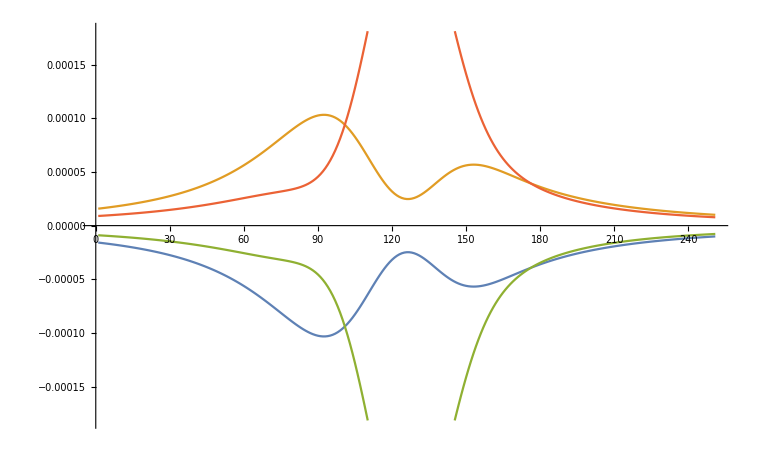

```mathematica
ListPlot[EitDP1test[100,1/1000,1.4/1000,0.1*10^6 ,0*10^6],Joined->True]
```

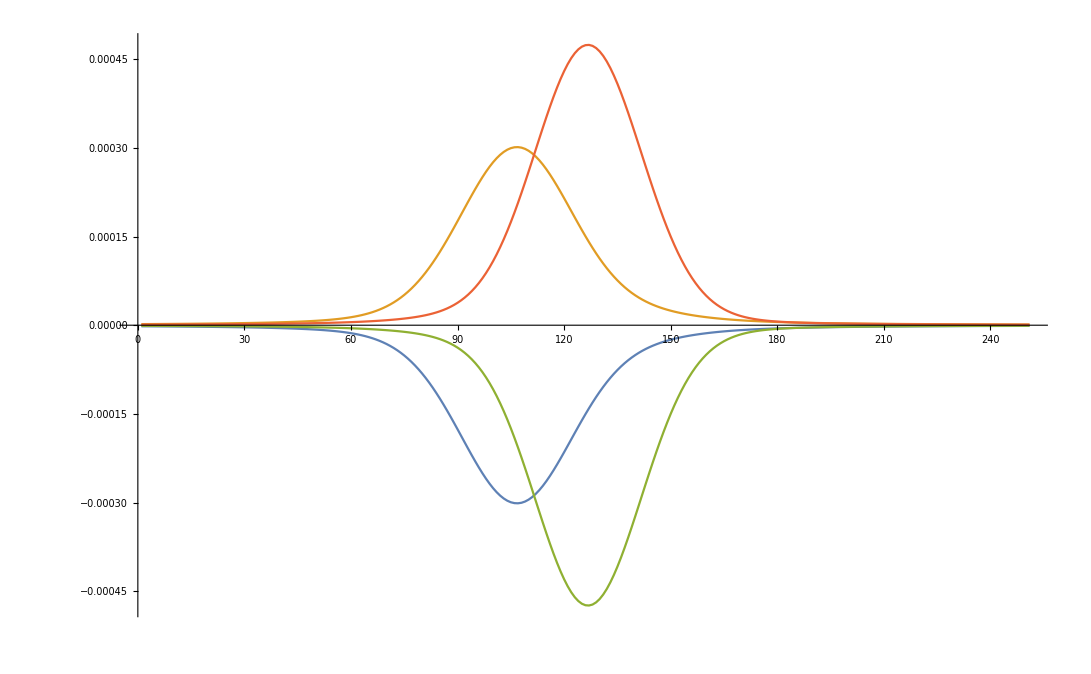

```mathematica
ListPlot[EitDP1test[100,1/1000,1.4/1000,1*10^6 ,0*10^6],Joined->True,PlotRange->All]
```

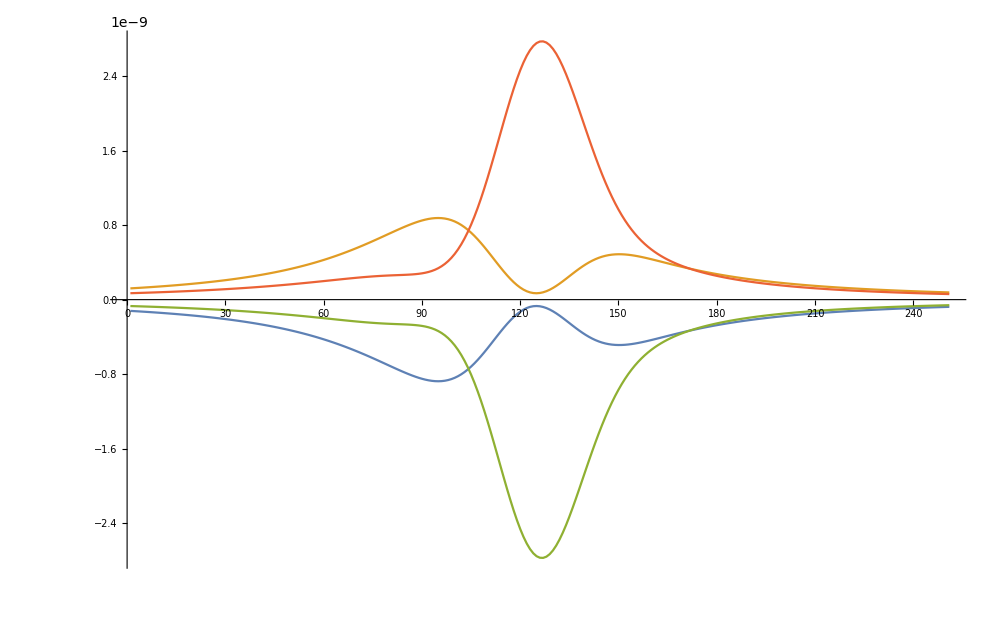

```mathematica
ListPlot[EitDP1test[-20,10/1000,1.4/1000,1*10^6 ,0*10^6],Joined->True,PlotRange->All]
```

```mathematica
Manipulate[
ListPlot[Evaluate[EitDP1test[T,P/1000,1.4/1000,γ*10^6 ,δ*10^6]],PlotRange->All,PlotStyle->{Blue,Darker[Blue],Red,Darker[Red]},GridLines->Automatic,Joined->True,Frame->True,Axes->False,FrameLabel-> {"ν-ν_o (GHz) ","transmission"},ImageSize->800]

,Style["Thoery",12,Bold],{{T,30,"T (C)"},0,60},{{P,0,"P(mW)"},0,10},{{γ,1,"γ(MHz)"},0,1},{{δ,0,"δ(MHz)"},-5,5,0.001}]
```

# Doppler Broadening Anayltically

```mathematica
χ42=(d42^2 Nat (16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))+4 √5 omegac1^2-5 √14 omegac1^2))/(5 e0 (8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))-7 ⅈ γ32 omegac1^2-2 ⅈ γ42 omegac1^2+9 δ omegac1^2+9 Δ omegac1^2+2 w43 (4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ))+omegac1^2)) ℏ);
χ32=(d32^2 Nat (40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))+35 omegac1^2-2 √70 omegac1^2))/(5 e0 (8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21(-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))-7 ⅈ γ32 omegac1^2-2 ⅈ γ42 omegac1^2+9 δ omegac1^2+9 Δ omegac1^2+2 w43 (4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ))+omegac1^2)) ℏ);
χ24=(d42^2 Nat (16 √5 γ32 δ+16 √5 γ21 (ⅈ γ32+δ+Δ)-ⅈ (16 √5 δ^2+16 √5 δ Δ-4 √5 omegac1^2+5 √14 omegac1^2)))/(5 e0 (8 ⅈ γ32 γ42 δ+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ-8 ⅈ δ Δ^2+8 γ21 (ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)-7 γ32 omegac1^2-2 γ42 omegac1^2+9 ⅈ δ omegac1^2+9 ⅈ Δ omegac1^2+w43 (8 γ32 δ+8 γ21 (ⅈ γ32+δ+Δ)-2 ⅈ (4 δ^2+4 δ Δ-omegac1^2))) ℏ);
χ23=(d32^2 Nat (40 √2 w43 (γ21-ⅈ δ)+40 √2 γ42 δ-40 ⅈ √2 δ^2-40 ⅈ √2 δ Δ+40 √2 γ21 (ⅈ γ42+δ+Δ)+35 ⅈ √2 omegac1^2-4 ⅈ √35 omegac1^2))/(5 √2 e0 (8 ⅈ γ32 γ42 δ+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ-8 ⅈ δ Δ^2+8 γ21 (ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)-7 γ32 omegac1^2-2 γ42 omegac1^2+9 ⅈ δ omegac1^2+9 ⅈ Δ omegac1^2+w43 (8 γ32 δ+8 γ21 (ⅈ γ32+δ+Δ)-2 ⅈ (4 δ^2+4 δ Δ-omegac1^2))) ℏ);
```

```mathematica
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify
s23=χ23/.Δ->Δ+wc v/c/.δ->δ;
s23=s23/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify
s24=χ24/.Δ->Δ+wc v/c/.δ->δ;
s24=s24/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify
```

(c d42^2 ⅇ^(-v^2/u^2) Nat (16 ⅈ √5 v wc (γ21+ⅈ δ)+c ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ)))))/(5 e0 √π u (8 ⅈ v^2 wc^2 (γ21+ⅈ δ)+c v wc (9 omegac1^2+8 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ+Δ)))+c^2 (8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 (δ+Δ)))) ℏ)

-((c d32^2 ⅇ^(-v^2/u^2) Nat ((-35+2 √70) c omegac1^2+40 v wc (-ⅈ γ21+δ)+40 c (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 √π u (8 ⅈ v^2 wc^2 (γ21+ⅈ δ)+c v wc (9 omegac1^2+8 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ+Δ)))+c^2 (8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 (δ+Δ)))) ℏ))

(c d32^2 ⅇ^(-v^2/u^2) Nat (-40 ⅈ √2 v wc (γ21-ⅈ δ)+c ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ))))/(5 e0 √(2 π) u (-8 ⅈ v^2 wc^2 (γ21-ⅈ δ)+c v wc (9 omegac1^2+8 (γ21-ⅈ δ) (-ⅈ w43+γ32+γ42-2 ⅈ (δ+Δ)))+c^2 (8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))+omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 (δ+Δ)))) ℏ)

(c d42^2 ⅇ^(-v^2/u^2) Nat (-16 ⅈ √5 v wc (γ21-ⅈ δ)+c ((4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (γ32-ⅈ (δ+Δ)))))/(5 e0 √π u (-8 ⅈ v^2 wc^2 (γ21-ⅈ δ)+c v wc (9 omegac1^2+8 (γ21-ⅈ δ) (-ⅈ w43+γ32+γ42-2 ⅈ (δ+Δ)))+c^2 (8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))+omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 (δ+Δ)))) ℏ)

```mathematica
Assuming[u> 0&&u∈Reals&&α1∉Reals&&α2∉Reals,Integrate[((v +Zα)ⅇ^(-v^2/u^2))/((v-α1)(v-α2)),{v,-∞,∞}]]
```

(-ⅇ^(-α1^2/u^2) (Zα+α1) (π Erfi[α1/u]-Log[-1/α1]-Log[α1])+ⅇ^(-α2^2/u^2) (Zα+α2) (π Erfi[α2/u]-Log[-1/α2]-Log[α2]))/(α1-α2)

```mathematica
Dopp[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=CoefficientList[num,v][[2]]/CoefficientList[den,v][[3]];
ans=Solve[den/CoefficientList[den,v][[3]]==0,v]//FullSimplify;
α1=ans[[1,1,2]];
α2=ans[[2,1,2]];
Zα=CoefficientList[num,v][[1]]/CoefficientList[num,v][[2]];
Int=A(-ⅇ^(-α1^2/u^2) (Zα+α1) (π Erfi[α1/u]-Log[-1/α1]-Log[α1])+ⅇ^(-α2^2/u^2) (Zα+α2) (π Erfi[α2/u]-Log[-1/α2]-Log[α2]))/(α1-α2)//Simplify
]
```

```mathematica
sd32[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s32]];
sd23[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s23]];
sd24[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s24]];
sd42[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s42]];
```

```mathematica
Lev4DoppTest[T_,P_,diam_,gam_,delt_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI},
d=Range[-1,1,0.0001]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 

Im[{sd24[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32],sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]
,sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32],sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]}]

]
```

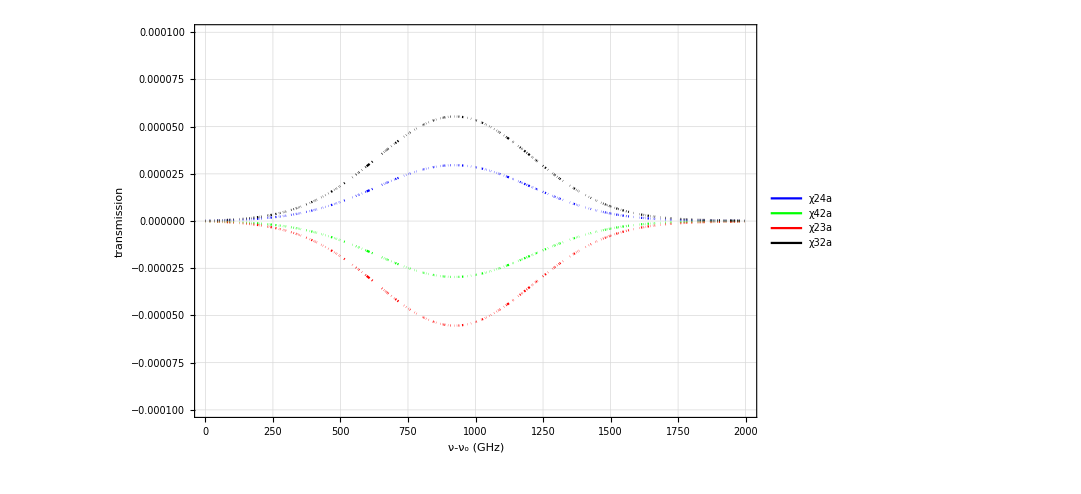

```mathematica
ListPlot[Evaluate[Lev4DoppTest[80,100/1000,1.4/1000,0.2*10^6 ,0*10^6]],PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Black,{Lighter[Red],Dashed},{Lighter[Orange],Dashed},{Lighter[Blue],Dashed},{Lighter[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{χ24a,χ42a,χ23a,χ32a,χ24n,χ42n,χ23n,χ32n},FrameLabel-> {"ν-ν_o (GHz) ","transmission"},ImageSize->800]
```

```mathematica
Manipulate[
ListPlot[
Evaluate[Lev4DoppTest[T,P/1000,1.4/1000,γ*10^6 ,δ*10^6]],PlotRange->{-0.001,0.001},PlotStyle->{Orange,Green,{Red,Dashed},{Black,Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"χ32","χ23","χ24","χ42"},FrameLabel-> {"ν-ν_o (GHz) ","transmission"},ImageSize->800]
,{T,10,100},{P,0,10},{γ,0.01,10},{{δ,0},-100,100}]
```

ListPlot::lpn: Lev4DoppTest[10.,0.,0.0014,10000.,0.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: Lev4DoppTest[10.,0.,0.0014,10000.,0.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: Lev4DoppTest[10.,0.,0.0014,10000.,0.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

## PLOT

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

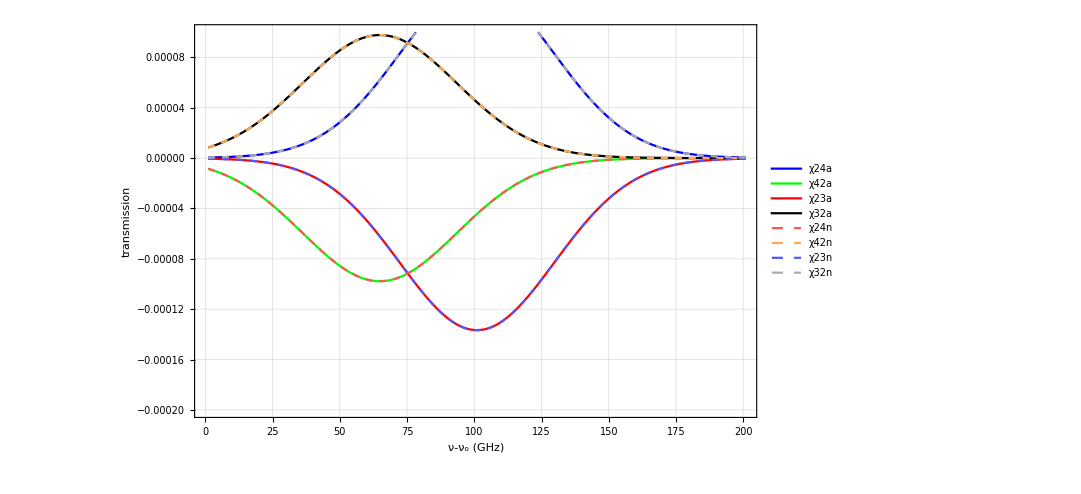

```mathematica
ListPlot[Flatten[{Evaluate[Lev4DoppTest[80,0/1000,1.4/1000,0.5*10^6 ,0*10^6]],Evaluate[EitDP1test[80,0/1000,1.4/1000,0.5*10^6 ,0*10^6]]},1],PlotRange->{-0.0002,0.0001},PlotStyle->{Blue,Green,Red,Black,{Lighter[Red],Dashed},{Lighter[Orange],Dashed},{Lighter[Blue],Dashed},{Lighter[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{χ24a,χ42a,χ23a,χ32a,χ24n,χ42n,χ23n,χ32n},FrameLabel-> {"ν-ν_o (GHz) ","transmission"},ImageSize->800]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

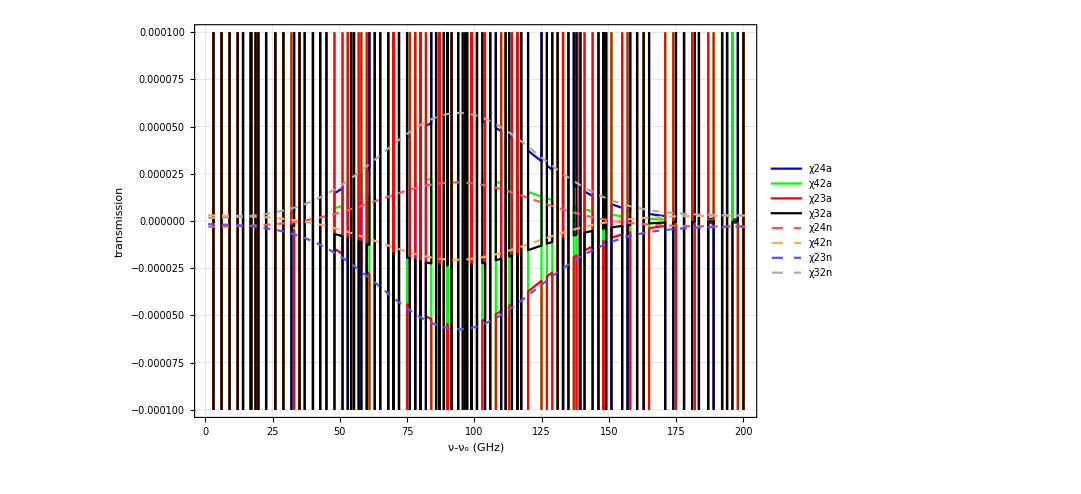

```mathematica
ListPlot[Flatten[{Evaluate[Lev4DoppTest[80,60/1000,1.4/1000,0.5*10^6 ,0*10^6]],Evaluate[EitDP1test[80,60/1000,1.4/1000,0.5*10^6 ,0*10^6]]},1],PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Black,{Lighter[Red],Dashed},{Lighter[Orange],Dashed},{Lighter[Blue],Dashed},{Lighter[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{χ24a,χ42a,χ23a,χ32a,χ24n,χ42n,χ23n,χ32n},FrameLabel-> {"ν-ν_o (GHz) ","transmission"},ImageSize->800]
```

```mathematica
ListPlot[Flatten[{Evaluate[Lev4DoppTest[80,100/1000,1.4/1000,0.2*10^6 ,0*10^6]],Evaluate[EitDP1test[80,100/1000,1.4/1000,0.2*10^6 ,0*10^6]]},1],PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Black,{Lighter[Red],Dashed},{Lighter[Orange],Dashed},{Lighter[Blue],Dashed},{Lighter[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{χ24a,χ42a,χ23a,χ32a,χ24n,χ42n,χ23n,χ32n},FrameLabel-> {"ν-ν_o (GHz) ","transmission"},ImageSize->800]
```

$Aborted[]

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted[]

$Aborted

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

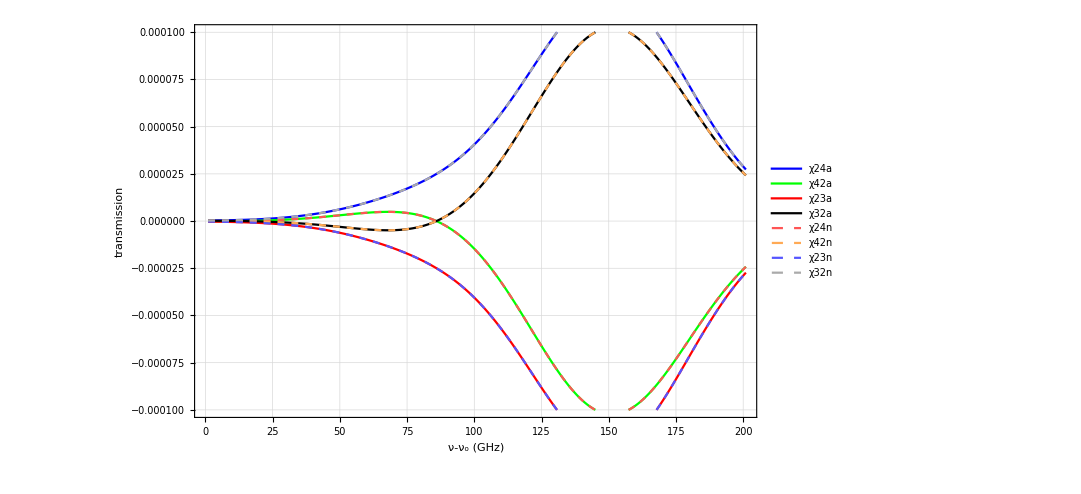

```mathematica
ListPlot[Flatten[{Evaluate[Lev4DoppTest[80,100/1000,1.4/1000,0.2*10^6 ,10*10^6]],Evaluate[EitDP1test[80,100/1000,1.4/1000,0.2*10^6 ,10*10^6]]},1],PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Black,{Lighter[Red],Dashed},{Lighter[Orange],Dashed},{Lighter[Blue],Dashed},{Lighter[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{χ24a,χ42a,χ23a,χ32a,χ24n,χ42n,χ23n,χ32n},FrameLabel-> {"ν-ν_o (GHz) ","transmission"},ImageSize->800]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

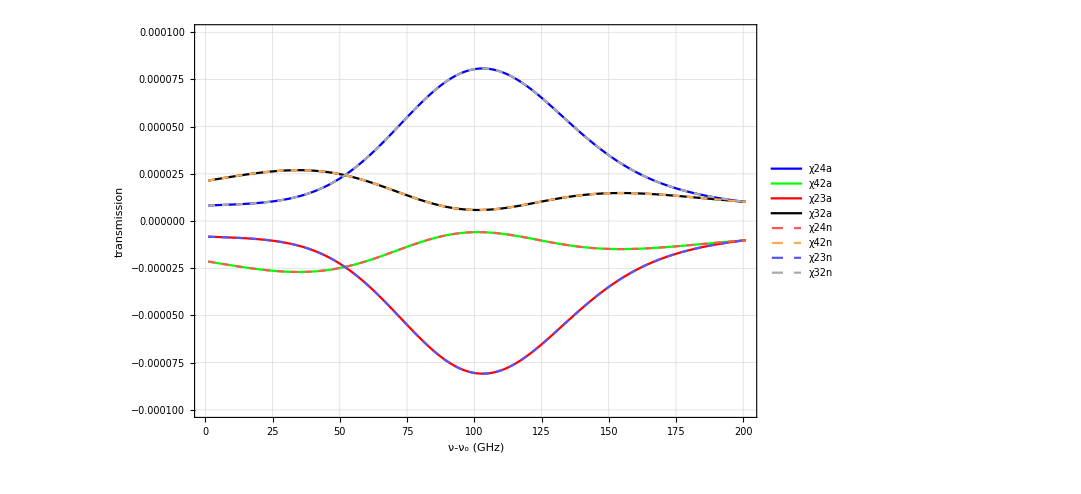

```mathematica
ListPlot[Flatten[{Evaluate[Lev4DoppTest[80,1/1000,1.4/1000,0.1*10^6 ,0*10^6]],Evaluate[EitDP1test[80,1/1000,1.4/1000,0.1*10^6 ,0*10^6]]},1],PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Black,{Lighter[Red],Dashed},{Lighter[Orange],Dashed},{Lighter[Blue],Dashed},{Lighter[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{χ24a,χ42a,χ23a,χ32a,χ24n,χ42n,χ23n,χ32n},FrameLabel-> {"ν-ν_o (GHz) ","transmission"},ImageSize->800]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

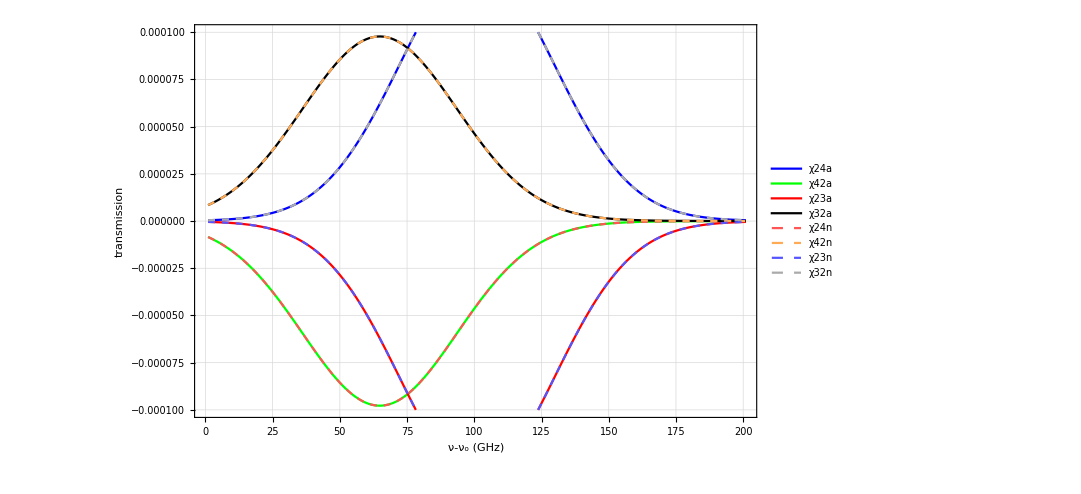

```mathematica
ListPlot[Flatten[{Evaluate[Lev4DoppTest[80,0/1000,1.4/1000,10*10^6 ,0*10^6]],Evaluate[EitDP1test[80,0/1000,1.4/1000,10*10^6 ,0*10^6]]},1],PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Black,{Lighter[Red],Dashed},{Lighter[Orange],Dashed},{Lighter[Blue],Dashed},{Lighter[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{χ24a,χ42a,χ23a,χ32a,χ24n,χ42n,χ23n,χ32n},FrameLabel-> {"ν-ν_o (GHz) ","transmission"},ImageSize->800]
```